```mathematica
Needs["MATLink`"]
OpenMATLAB[]
MEvaluate["cd '/Users/kn328/Matlab_Numerics/Victor_SDP'"]
```

```mathematica
(*Kept

OptDecode.m 
OptEncode.m 
PTr.m 
Qfunction.m 
Qprimefunction.m

at /Users/kn328/Matlab_Numerics/Victor_SDP *)
```

```mathematica
1. Modules
```

```mathematica
(a) Code manipulation and characterization
```

```mathematica
(a1) Code manipulation
```

```mathematica
Columnize[Input_]:=Table[{Input[[i]]},{i,1,Length[Input]}]
DeColumnize[Input_]:=Table[Input[[i]][[1]],{i,1,Length[Input]}]
```

```mathematica
(a2) Code characterization
```

```mathematica
Displacement[α_,Cutoff_]:=Exp[-Abs[α]^2/2]*If[α==0,IdentityMatrix[Cutoff],Table[If[i≥j,Sqrt[Factorial[j-1]/Factorial[i-1]]*LaguerreL[j-1,i-j,Abs[α]^2]*α^(i-j),Sqrt[Factorial[i-1]/Factorial[j-1]]*LaguerreL[i-1,j-i,Abs[α]^2]*(-Conjugate[α])^(j-i)],{i,1,Cutoff},{j,1,Cutoff}]]
WignerFunctionFromStateColumn[x_,Cutoff_,Input_]:=Module[{RawDensityMatrix,DensityMatrix,ParityOperator,Return},RawDensityMatrix=Input.ConjugateTranspose[Input];
DensityMatrix=Table[If[i≤Length[RawDensityMatrix]&&j≤Length[RawDensityMatrix],RawDensityMatrix[[i,j]],0],{i,1,Cutoff},{j,1,Cutoff}];ParityOperator=Table[KroneckerDelta[i,j]*(-1)^(i-1),{i,1,Cutoff},{j,1,Cutoff}];Return=Tr[Displacement[-x/Sqrt[2],Cutoff].DensityMatrix.Displacement[x/Sqrt[2],Cutoff].ParityOperator]/Pi;Return]
WignerFunctionFromDensityMatrix[x_,Cutoff_,Input_]:=Module[{DensityMatrix,ParityOperator,Return},DensityMatrix=Table[If[i≤Length[Input]&&j≤Length[Input],Input[[i,j]],0],{i,1,Cutoff},{j,1,Cutoff}];ParityOperator=Table[KroneckerDelta[i,j]*(-1)^(i-1),{i,1,Cutoff},{j,1,Cutoff}];Return=Tr[Displacement[-x/Sqrt[2],Cutoff].DensityMatrix.Displacement[x/Sqrt[2],Cutoff].ParityOperator]/Pi;Return]
BlueRed[x_,xmin_,xmax_]:=Blend[{
{xmin+1.0*(xmax-xmin), RGBColor[0.40392156862745099,0.0,0.12156862745098039]}, {xmin+0.9*(xmax-xmin),RGBColor[0.69803921568627447,0.09411764705882353,0.16862745098039217]},
 {xmin+0.8*(xmax-xmin),RGBColor[0.83921568627450982,0.37647058823529411,0.30196078431372547]}, 
{xmin+0.7*(xmax-xmin), RGBColor[0.95686274509803926,0.6470588235294118,0.50980392156862742]},
{xmin+0.6*(xmax-xmin), RGBColor[0.99215686274509807,0.85882352941176465,0.7803921568627451]},
{xmin+0.5*(xmax-xmin), White}, 
{xmin+0.4*(xmax-xmin), RGBColor[0.81960784313725488,0.89803921568627454,0.94117647058823528]},
{xmin+0.3*(xmax-xmin), RGBColor[0.5725490196078431,0.77254901960784317,0.87058823529411766]},
{xmin+0.2*(xmax-xmin),RGBColor[0.2627450980392157,0.57647058823529407,0.76470588235294112]},
{xmin+0.1*(xmax-xmin), RGBColor[0.12941176470588237,0.4,0.67450980392156867]},{xmin+0.0*(xmax-xmin),RGBColor[0.0196078431372549,0.18823529411764706,0.38039215686274508]}}, x]
PlotWigner[StateInput_,Color_Symbol,ColorMin_,ColorMax_,Cutoff_,PlotPoint_]:=DensityPlot[Re[WignerFunctionFromStateColumn[x+I*y,Cutoff,StateInput]],{x,-4.5,4.5},{y,-4.5,4.5},ColorFunction->(Color[#,ColorMin,ColorMax]&),ColorFunctionScaling->False,PlotRange->{ColorMin,ColorMax},PlotLegends->BarLegend[{Color[#,ColorMin,ColorMax]&,{ColorMin,ColorMax}}],PlotPoints->PlotPoint,Frame->True,FrameTicksStyle->Directive[FontSize->18,FontFamily->"Times New Roman"],FrameTicks->{{{-4,None,-2,None,0,None,2,None,4},None},{{-4,None,-2,None,0,None,2,None,4},None}},FrameLabel->{Style["q",FontSize->24,FontFamily->"Times New Roman"],Style["p",FontSize->24,FontFamily->"Times New Roman"]},RotateLabel->False]
PlotWignerFromDensityMatrix[StateInput_,Color_Symbol,ColorMin_,ColorMax_,Cutoff_,PlotPoint_]:=DensityPlot[Re[WignerFunctionFromDensityMatrix[x+I*y,Cutoff,StateInput]],{x,-4.5,4.5},{y,-4.5,4.5},ColorFunction->(Color[#,ColorMin,ColorMax]&),ColorFunctionScaling->False,PlotRange->{ColorMin,ColorMax},PlotLegends->BarLegend[{Color[#,ColorMin,ColorMax]&,{ColorMin,ColorMax}}],PlotPoints->PlotPoint,Frame->True,FrameTicksStyle->Directive[FontSize->18,FontFamily->"Times New Roman"],FrameTicks->{{{-4,None,-2,None,0,None,2,None,4},None},{{-4,None,-2,None,0,None,2,None,4},None}},FrameLabel->{Style["q",FontSize->24,FontFamily->"Times New Roman"],Style["p",FontSize->24,FontFamily->"Times New Roman"]},RotateLabel->False]
```

```mathematica
(b) Choi matrix from Kraus operators
```

```mathematica
ToVector[op_]:=ArrayReshape[Transpose[op],{Length[op]Length[op[[1]]],1}]
RepCho[SetOfKruas_]:=Sum[ToVector[SetOfKruas[[i]]].ConjugateTranspose[ToVector[SetOfKruas[[i]]]],{i,1,Length[SetOfKruas]}]
```

```mathematica
(b1) Choi matrix of bosonic error channels
```

```mathematica
a[nm_]:=Table[If[ii==jj-1,√(ii+1),0],{ii,0,nm-1},{jj,0,nm-1}]
ad[nm_]:=Transpose[a[nm]]
Ph[nm_]:=DiagonalMatrix[Table[m,{m,0,nm-1}]]
EE[nm_,l_,γ_]:=If[l==0,MatrixExp[1/2 Log[1-γ]*Ph[nm]],√(γ^l/(l!))MatrixExp[1/2 Log[1-γ] Ph[nm]].MatrixPower[a[nm],l]]
```

```mathematica
KrausSetSynthesizedChannel[KrausSetPost_,KrausSetPre_]:=If[Length[KrausSetPre]==1,Table[KrausSetPost[[i]].KrausSetPre[[1]],{i,1,Length[KrausSetPost]}],Table[KrausSetPost[[IntegerDigits[i-1,Length[KrausSetPre],2][[1]]+1]].KrausSetPre[[IntegerDigits[i-1,Length[KrausSetPre],2][[2]]+1]],{i,1,Length[KrausSetPost]*Length[KrausSetPre]}]]
```

```mathematica
KrausSetPureLoss[nmax_,HighestOrder_,η_]:=Table[EE[nmax,l,1-η],{l,0,HighestOrder-1}]
KrausSetAmplification[nmax_,HighestOrder_,G_]:=Table[√(1/G)Transpose[EE[nmax,l,(G-1)/G]],{l,0,HighestOrder-1}]
KrausSetThermalLoss[nmax_,HighestOrderAmp_,HighestOrderPureLoss_,η_,nth_]:=KrausSetSynthesizedChannel[KrausSetAmplification[nmax,HighestOrderAmp,(1-η)nth+1],KrausSetPureLoss[nmax,HighestOrderPureLoss,η/((1-η)nth+1)]]
KrausSetDisplacementOption2[nmax_,HighestOrderAmp_,HighestOrderPureLoss_,σ_]:=KrausSetSynthesizedChannel[KrausSetAmplification[nmax,HighestOrderAmp,1+σ^2],KrausSetPureLoss[nmax,HighestOrderPureLoss,1/(1+σ^2)]]
KrausSetDephasing[nmax_,HighestOrder_,σϕ_]:=Table[σϕ^k/(√(k!))MatrixExp[-1/2 σϕ^2 *MatrixPower[Ph[nmax],2]].If[k==0,IdentityMatrix[nmax],MatrixPower[Ph[nmax],k]],{k,0,HighestOrder}]
```

```mathematica
PhotonLossChoi[γ_,nmax_]:=RepCho[Table[EE[nmax,l,γ],{l,0,nmax-1}]]
ThermalLossChoi[η_,nth_,AmpCutoff_,nmax_]:=RepCho[KrausSetThermalLoss[nmax,AmpCutoff,nmax,η,nth]]
DisplacementChoi[σ_,AmpCutoff_,nmax_]:=RepCho[KrausSetDisplacementOption2[nmax,AmpCutoff,nmax,σ]]
DephasingChoi[σϕ_,nmax_]:=Sum[KroneckerProduct[Table[If[k==i&&l==j,1,0],{k,1,nmax},{l,1,nmax}],Table[If[k==i&&l==j,Exp[-σϕ^2(i-j)^2/2],0],{k,1,nmax},{l,1,nmax}]],{i,1,nmax},{j,1,nmax}]
```

```mathematica
(b2) Choi matrix of qubit error channels
```

```mathematica
KroneckerProductFromTable[InputTable_]:=Module[{PreReturn,Return},PreReturn=InputTable[[1]];For[i=2,i≤ Length[InputTable],i++,PreReturn=KroneckerProduct[PreReturn,InputTable[[i]]]];Return=PreReturn]
MultiQubitKrausFromSingleQubit[InputKrausSet_,NumberOfQubits_]:=Module[{MultiQubitKrausSet,Return},MultiQubitKrausSet=Table[Table[InputKrausSet[[IntegerDigits[i-1,Length[InputKrausSet],NumberOfQubits][[j]]+1]],{j,1,NumberOfQubits}],{i,1,Length[InputKrausSet]^NumberOfQubits}];Return=Table[KroneckerProductFromTable[MultiQubitKrausSet[[i]]],{i,1,Length[InputKrausSet]^NumberOfQubits}]]
```

```mathematica
KrausSetAmplitudeDamping[γ_]:={({{1, 0}, {0, √(1-γ)}}),({{0, √γ}, {0, 0}})}
MultiQubitKrausSetAmplitudeDamping[γ_,NumberOfQubits_]:=MultiQubitKrausFromSingleQubit[KrausSetAmplitudeDamping[γ],NumberOfQubits]
MultiQubitAmplitudeDampingChoi[γ_,NumberOfQubits_]:=RepCho[MultiQubitKrausSetAmplitudeDamping[γ,NumberOfQubits]]
```

```mathematica
KrausSetDepolarization[p_]:={({{√(1-(3p)/4), 0}, {0, √(1-(3p)/4)}}),√(p/4)({{1, 0}, {0, -1}}),√(p/4)({{0, 1}, {1, 0}}),√(p/4)({{0, -I}, {I, 0}})}
MultiQubitKrausSetDepolarization[p_,NumberOfQubits_]:=MultiQubitKrausFromSingleQubit[KrausSetDepolarization[p],NumberOfQubits]
MultiQubitDepolarizationChoi[p_,NumberOfQubits_]:=RepCho[MultiQubitKrausSetDepolarization[p,NumberOfQubits]]
```

```mathematica
(c) Optimization
```

```mathematica
(c0) Conversion between encoding choi and logical states
```

```mathematica
EncodingChoiFromCode[states_]:=Columnize[Catenate[states]].ConjugateTranspose[Columnize[Catenate[states]]]
EncodingChoiToCodeAdjustableMaxTol[d_,n_,EncodingChoi_,MaxTol_]:=If[Abs[Eigenvalues[EncodingChoi][[1]]-d]/d>MaxTol,Print["Code not isometry"],Table[Sqrt[Eigenvalues[EncodingChoi][[1]]]*Table[Eigenvectors[EncodingChoi][[1]][[j+n*(i-1)]],{j,1,n}],{i,1,d}]]
CodeProjection[InputCode_]:=Sum[Columnize[InputCode[[i]]].ConjugateTranspose[Columnize[InputCode[[i]]]],{i,1,Length[InputCode]}]/Length[InputCode]
NbarCode[InputCode_]:=Sum[CodeProjection[InputCode][[n,n]]*(n-1),{n,1,Length[CodeProjection[InputCode]]}]
```

```mathematica
(c1) Decoding optimization
```

```mathematica
OptDecode[d_,n_,EncodingChoi_,NoisyChannelChoi_]:=Module[{Return},MSet["d",d];MSet["n",n];MSet["LossChoi",NoisyChannelChoi];MSet["EncodingChoi",EncodingChoi];
MEvaluate["[Infid, DecodingChoiout] = OptDecode(d,n,LossChoi,EncodingChoi)"];Return={MGet["Infid"],MGet["DecodingChoiout"]}]
```

```mathematica
Example : single mode bosonic code
```

```mathematica
(*Code should be saved in the form {logical state 1, logical state 2, ...} where each logical state is a row vector*)
```

```mathematica
bin11={1/(√2){1,0,0,0,1},{0,0,1,0,0}};
sqrt17={1/(√6){√(7-√17),0,0,√(√17-1),0},1/(√6){0,√(9-√17),0,0,-√(√17-3)}};
bin20={1/2{1,0,√3,0},1/2{0,√3,0,1}};
```

```mathematica
GKPnbar3N30={{0.04330280636782234-0.0055384188759030365 ⅈ,-0.564733487138371-0.48615292595168846 ⅈ,-0.04142631788554501-0.002983144011055789 ⅈ,0.09046434055052538+0.015578760183298337 ⅈ,-0.31194326461160143+0.4830228187619822 ⅈ,0.013061240924322502+0.04651897091419684 ⅈ,-0.009708570967518999+0.03870398301408778 ⅈ,-0.07118832655272968-0.031441122458653145 ⅈ,-0.008641485912908165+0.00048762314388696795 ⅈ,-0.0073716953742625786+0.028330110709780813 ⅈ,0.07083690019253341-0.2113604521638049 ⅈ,-0.01532650387576243-0.025989151416942132 ⅈ,-0.022850619523250085-0.029082524420687688 ⅈ,0.16895591878312044+0.03041268423314005 ⅈ,0.02432869304786334-0.01570571782194103 ⅈ,-0.011329008829954374+0.009681170003741179 ⅈ,0.0027588133306071716-0.06994615386828901 ⅈ,-0.007607925801037567-0.012175137175682926 ⅈ,0.007986240878089306+0.015538283560228305 ⅈ,-0.0458273879522144+0.005282280592211608 ⅈ,-0.004901446721701516+0.00835954833116187 ⅈ,-0.006751932515839381+0.008118635593777863 ⅈ,-0.006065011446513552-0.024015494513409518 ⅈ,-0.004604644598138185-0.0032299840712365956 ⅈ,0.004608348183565468+0.00204406668182696 ⅈ,-0.012929689100998098+0.004890303232195606 ⅈ,-0.0006354449456264938+0.0026132591761133138 ⅈ,-0.0009204710317149413+0.0008029440028638529 ⅈ,-0.002119156469834238-0.0036266609082663288 ⅈ,-0.0021319406931913365-0.0009477069117785888 ⅈ},{0.5576247577730811+0.3632915397404396 ⅈ,-0.008599052276840371+0.05055994174482707 ⅈ,0.04320773343930241-0.012860254282750557 ⅈ,-0.23430115791510428+0.47621935540541316 ⅈ,0.058680579535046296+0.05471020598066408 ⅈ,0.026570535312318188+0.038963509467833286 ⅈ,-0.34712751608146575-0.11500804138577143 ⅈ,-0.03865762334987961+0.021993402861187547 ⅈ,0.042488161843099705-0.027495182757764344 ⅈ,-0.05827144769284587+0.3280777448600032 ⅈ,0.005872952484157228+0.0336456301441443 ⅈ,0.003035112720835807+0.004664338204183689 ⅈ,-0.013306240038894517+0.001968182038553997 ⅈ,-0.0023267512758217822-0.01274313645605379 ⅈ,-0.00024255146454054647-0.0033604831362921703 ⅈ,0.0020714469950737675+0.013410768674669697 ⅈ,-0.00394047016174215+0.0003231415135828667 ⅈ,0.019025205366137193+0.013459185435514606 ⅈ,-0.0908922822629405+0.019454973625564528 ⅈ,-0.007957670109270247+0.019431829611932402 ⅈ,-0.0021304224766212983+0.009211135056447958 ⅈ,-0.010364397797297888-0.03008725855293967 ⅈ,-0.009369696335327327-0.002265225083759408 ⅈ,-0.0030633491338403593+0.00018748048170045398 ⅈ,0.004852203763822798-0.0028584975826365876 ⅈ,0.0011676155065669105+0.0010666226259286847 ⅈ,-0.0004963201403770144+0.005853182906581222 ⅈ,-0.006101033805460839-0.008717236488902524 ⅈ,-0.001010387204521428-0.00006275402553430192 ⅈ,0.002401026603389205+0. ⅈ}};
```

```mathematica
Bosonic-pure loss channel
```

```mathematica
CodeEval=bin11;
```

```mathematica
Infidelitybin11=Table[{γ,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],PhotonLossChoi[γ,Length[CodeEval[[1]]]]][[1]]},{γ,0.01,0.1,0.01}]
```

{{0.01,0.000186253},{0.02,0.000740055},{0.03,0.00165403},{0.04,0.00292087},{0.05,0.00453337},{0.06,0.00648438},{0.07,0.00876683},{0.08,0.0113737},{0.09,0.0142981},{0.1,0.0175332}}

```mathematica
CodeEval=sqrt17;
```

```mathematica
Infidelitysqrt17=Table[{γ,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],PhotonLossChoi[γ,Length[CodeEval[[1]]]]][[1]]},{γ,0.01,0.1,0.01}]
```

{{0.01,0.000127611},{0.02,0.000512918},{0.03,0.00115905},{0.04,0.00206839},{0.05,0.00324266},{0.06,0.00468294},{0.07,0.00638972},{0.08,0.00836294},{0.09,0.0106021},{0.1,0.0131061}}

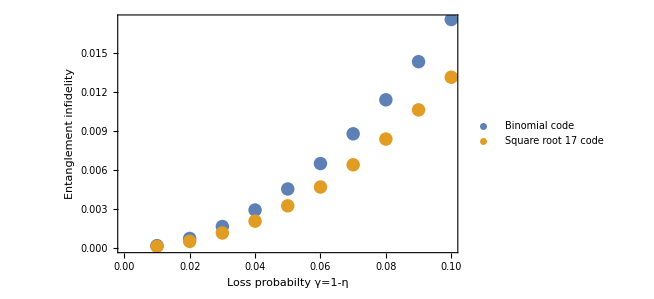

```mathematica
ListPlot[{Infidelitybin11,Infidelitysqrt17},Frame->True,FrameTicksStyle->Directive[20],FrameStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.02]},{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.02]}},PlotLegends->Placed[{Style["Binomial code",FontSize->15,FontFamily->"Times New Roman"],Style["Square root 17 code",FontSize->15,FontFamily->"Times New Roman"]},{Left,Top}],FrameLabel->{Style["Loss probabilty γ=1-η",FontSize->20,FontFamily->"Times New Roman"],Style["Entanglement infidelity",FontSize->20,FontFamily->"Times New Roman"]}]
```

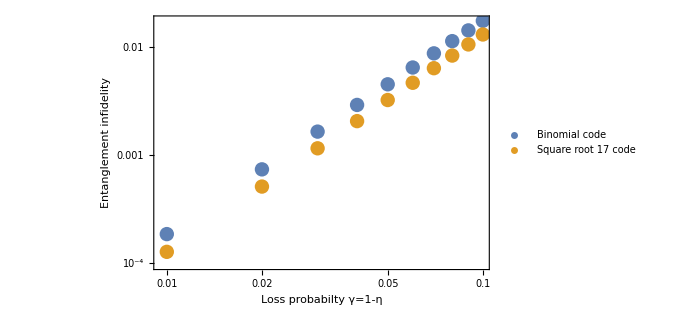

```mathematica
ListLogLogPlot[{Infidelitybin11,Infidelitysqrt17},Frame->True,FrameTicksStyle->Directive[20],FrameStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.02]},{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.02]}},PlotLegends->Placed[{Style["Binomial code",FontSize->15,FontFamily->"Times New Roman"],Style["Square root 17 code",FontSize->15,FontFamily->"Times New Roman"]},{Left,Top}],FrameLabel->{Style["Loss probabilty γ=1-η",FontSize->20,FontFamily->"Times New Roman"],Style["Entanglement infidelity",FontSize->20,FontFamily->"Times New Roman"]}]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
Dephasing
```

```mathematica
CodeEval=bin11;
```

```mathematica
Infidelitybin11Dephasing=Table[{DephasingVar,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],DephasingChoi[Sqrt[DephasingVar],Length[CodeEval[[1]]]]][[1]]},{DephasingVar,0.01,0.1,0.01}]
```

{{0.01,0.00990066},{0.02,0.0196053},{0.03,0.0291177},{0.04,0.0384418},{0.05,0.0475813},{0.06,0.0565398},{0.07,0.0653209},{0.08,0.0739281},{0.09,0.0823649},{0.1,0.0906346}}

```mathematica
CodeEval=bin20;
```

```mathematica
Infidelitybin20Dephasing=Table[{DephasingVar,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],DephasingChoi[Sqrt[DephasingVar],Length[CodeEval[[1]]]]][[1]]},{DephasingVar,0.01,0.1,0.01}]
```

{{0.01,0.0000374835},{0.02,0.000149744},{0.03,0.000336241},{0.04,0.000596136},{0.05,0.00092834},{0.06,0.00133155},{0.07,0.00180429},{0.08,0.00234495},{0.09,0.00295177},{0.1,0.00362295}}

```mathematica
CodeEval=sqrt17;
```

```mathematica
Infidelitysqrt17Dephasing=Table[{DephasingVar,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],DephasingChoi[Sqrt[DephasingVar],Length[CodeEval[[1]]]]][[1]]},{DephasingVar,0.01,0.1,0.01}]
```

{{0.01,0.000374434},{0.02,0.000956996},{0.03,0.00174355},{0.04,0.0027272},{0.05,0.00389905},{0.06,0.00524885},{0.07,0.0067655},{0.08,0.0084374},{0.09,0.0102528},{0.1,0.0121999}}

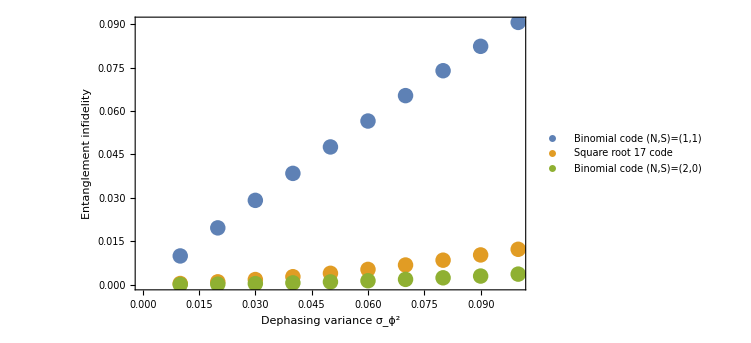

```mathematica
ListPlot[{Infidelitybin11Dephasing,Infidelitysqrt17Dephasing,Infidelitybin20Dephasing},Frame->True,FrameTicksStyle->Directive[20],FrameStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.02]},{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.02]},{RGBColor[0.560181, 0.691569, 0.194885],PointSize[0.02]}},PlotLegends->Placed[{Style["Binomial code (N,S)=(1,1)",FontSize->15,FontFamily->"Times New Roman"],Style["Square root 17 code",FontSize->15,FontFamily->"Times New Roman"],Style["Binomial code (N,S)=(2,0)",FontSize->15,FontFamily->"Times New Roman"]},{Left,Top}],FrameLabel->{Style["Dephasing variance σ_ϕ^2",FontSize->20,FontFamily->"Times New Roman"],Style["Entanglement infidelity",FontSize->20,FontFamily->"Times New Roman"]}]
```

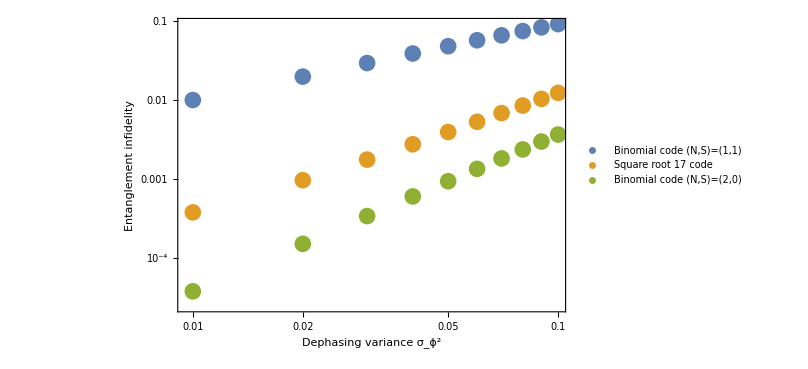

```mathematica
ListLogLogPlot[{Infidelitybin11Dephasing,Infidelitysqrt17Dephasing,Infidelitybin20Dephasing},Frame->True,FrameTicksStyle->Directive[20],FrameStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.02]},{RGBColor[0.880722, 0.611041, 0.142051],PointSize[0.02]},{RGBColor[0.560181, 0.691569, 0.194885],PointSize[0.02]}},PlotLegends->Placed[{Style["Binomial code (N,S)=(1,1)",FontSize->15,FontFamily->"Times New Roman"],Style["Square root 17 code",FontSize->15,FontFamily->"Times New Roman"],Style["Binomial code (N,S)=(2,0)",FontSize->15,FontFamily->"Times New Roman"]},{Right,Bottom}],FrameLabel->{Style["Dephasing variance σ_ϕ^2",FontSize->20,FontFamily->"Times New Roman"],Style["Entanglement infidelity",FontSize->20,FontFamily->"Times New Roman"]}]
```

```mathematica
CodeEval=GKPnbar3N30;
```

```mathematica
InfidelityGKP3Dephasing=Table[{DephasingVar,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],DephasingChoi[Sqrt[DephasingVar],Length[CodeEval[[1]]]]][[1]]},{DephasingVar,0.01,0.1,0.01}]
```

{{0.01,0.00103886},{0.02,0.0031371},{0.03,0.00548353},{0.04,0.00783796},{0.05,0.0102077},{0.06,0.0126187},{0.07,0.0150771},{0.08,0.0175758},{0.09,0.0201026},{0.1,0.0226451}}

```mathematica
Example : 5 qubit stabilizer code
```

```mathematica
Zero=({{1}, {0}});
One=({{0}, {1}});
X=({{0, 1}, {1, 0}});
```

```mathematica
FiveQubitCodeLogicalZero=1/4(KroneckerProduct[Zero,Zero,Zero,Zero,Zero]+KroneckerProduct[One,Zero,Zero,One,Zero]+KroneckerProduct[Zero,One,Zero,Zero,One]+KroneckerProduct[One,Zero,One,Zero,Zero]+KroneckerProduct[Zero,One,Zero,One,Zero]-KroneckerProduct[One,One,Zero,One,One]-KroneckerProduct[Zero,Zero,One,One,Zero]-KroneckerProduct[One,One,Zero,Zero,Zero]-KroneckerProduct[One,One,One,Zero,One]-KroneckerProduct[Zero,Zero,Zero,One,One]-KroneckerProduct[One,One,One,One,Zero]-KroneckerProduct[Zero,One,One,One,One]-KroneckerProduct[One,Zero,Zero,Zero,One]-KroneckerProduct[Zero,One,One,Zero,Zero]-KroneckerProduct[One,Zero,One,One,One]+KroneckerProduct[Zero,Zero,One,Zero,One]);
FiveQubitCode={DeColumnize[FiveQubitCodeLogicalZero],DeColumnize[KroneckerProduct[X,X,X,X,X].FiveQubitCodeLogicalZero]};
```

```mathematica
CodeEval=FiveQubitCode;
```

```mathematica
InfidelityFiveQubitCode=Table[{γ,OptDecode[Length[CodeEval],Length[CodeEval[[1]]],EncodingChoiFromCode[CodeEval],MultiQubitAmplitudeDampingChoi[γ,Log[2,Length[CodeEval[[1]]]]]][[1]]},{γ,0.01,0.1,0.01}]
```

{{0.01,0.000116856},{0.02,0.000468227},{0.03,0.00105522},{0.04,0.00187883},{0.05,0.00293989},{0.06,0.00423916},{0.07,0.00577723},{0.08,0.00755458},{0.09,0.00957157},{0.1,0.0118284}}

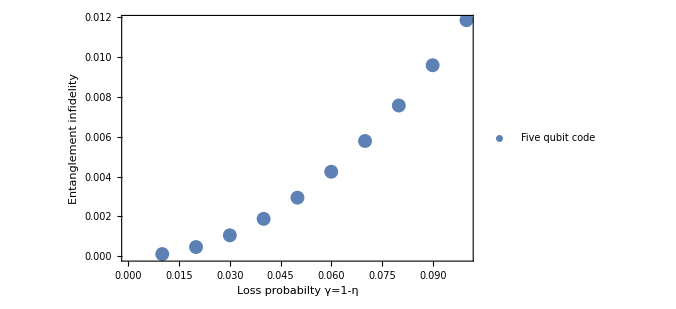

```mathematica
ListPlot[InfidelityFiveQubitCode,Frame->True,FrameTicksStyle->Directive[20],FrameStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],PointSize[0.02]}},PlotLegends->Placed[{Style["Five qubit code",FontSize->15,FontFamily->"Times New Roman"]},{Left,Top}],FrameLabel->{Style["Loss probabilty γ=1-η",FontSize->20,FontFamily->"Times New Roman"],Style["Entanglement infidelity",FontSize->20,FontFamily->"Times New Roman"]}]
```

```mathematica
(c2) Encoding optimization
```

```mathematica
OptEncode[d_,n_,NbarCon_,DecodingChoi_,NoisyChannelChoi_]:=Module[{Return},MSet["d",d];MSet["n",n];
MSet["NbarCon",NbarCon];
MSet["LossChoi",NoisyChannelChoi];MSet["DecodingChoi",DecodingChoi];
MEvaluate["[Infid, EncodingChoiout,Nbar] = OptEncode(d,n,NbarCon,LossChoi,DecodingChoi)"];Return={MGet["Infid"],MGet["EncodingChoiout"],MGet["Nbar"]}]
```

```mathematica
(c3) Random code generation
```

```mathematica
RandomCode[d_,n_]:=Module[{RR,RC,RG,RU,RUSaved,Return},RR:=RandomReal[NormalDistribution[0,1]];RC:=RR+I*RR;RG:=Table[RC,{n},{n}];RU:=Orthogonalize[RG];RUSaved=RU;Return=Table[RUSaved[[i]],{i,1,d}]]
```

```mathematica
RandomCodeBosonicN30d2=RandomCode[2,30]
```

{{0.0131875-0.0683527 ⅈ,0.0727453-0.0767313 ⅈ,0.0821745+0.0251735 ⅈ,-0.0943708+0.297512 ⅈ,0.0808623+0.0735482 ⅈ,0.133443-0.0138228 ⅈ,-0.035995-0.200334 ⅈ,0.157385+0.139917 ⅈ,-0.022688-0.453104 ⅈ,0.176913+0.0349332 ⅈ,0.0442485-0.131099 ⅈ,-0.0550341+0.0147997 ⅈ,-0.082012+0.0491173 ⅈ,0.0247612+0.223123 ⅈ,-0.0661338+0.12976 ⅈ,0.157447+0.00556144 ⅈ,-0.142808-0.0310149 ⅈ,-0.193241-0.00642853 ⅈ,-0.174569+0.0547547 ⅈ,-0.118694+0.0641372 ⅈ,-0.16818+0.0364918 ⅈ,-0.138075+0.0671879 ⅈ,-0.139635+0.0665979 ⅈ,-0.125184-0.00882462 ⅈ,0.0567912+0.0688929 ⅈ,-0.249172+0.175971 ⅈ,0.0186416+0.0330961 ⅈ,0.278145-0.0702585 ⅈ,-0.00377116-0.0118463 ⅈ,0.0121015-0.0937608 ⅈ},{-0.166703-0.0136249 ⅈ,0.323113-0.237905 ⅈ,0.07543-0.0828772 ⅈ,-0.0676903+0.169676 ⅈ,-0.116197-0.0073557 ⅈ,0.0680262-0.0178471 ⅈ,-0.0440184+0.027834 ⅈ,-0.111632+0.024331 ⅈ,0.0772989-0.100733 ⅈ,-0.0442841+0.0810654 ⅈ,-0.0481608-0.178692 ⅈ,0.118144+0.0379941 ⅈ,-0.134842-0.0507807 ⅈ,-0.034718-0.17744 ⅈ,0.0282636-0.106048 ⅈ,0.248875-0.0141757 ⅈ,0.265083+0.0293536 ⅈ,-0.0964597+0.0787509 ⅈ,0.161212-0.09706 ⅈ,0.174641-0.0947506 ⅈ,-0.0835839+0.0957558 ⅈ,-0.0102603+0.00617944 ⅈ,-0.0101617+0.019521 ⅈ,0.123532+0.251707 ⅈ,0.00241323+0.199239 ⅈ,0.217006-0.0649634 ⅈ,0.0429256+0.0470653 ⅈ,-0.0416742-0.0728217 ⅈ,-0.207997+0.143311 ⅈ,0.325568-0.00718915 ⅈ}}

```mathematica
RandomCodeMultiQubitN5d2=RandomCode[2,2^5]
```

{{-0.198499-0.190789 ⅈ,-0.0531104+0.00533262 ⅈ,-0.0201247+0.003539 ⅈ,0.0722555-0.0177071 ⅈ,0.104126+0.100827 ⅈ,-0.11196-0.0836498 ⅈ,0.328964-0.142095 ⅈ,-0.229928+0.0183532 ⅈ,0.0977065+0.0183693 ⅈ,-0.00207954-0.100825 ⅈ,0.131388-0.0682945 ⅈ,-0.0896753-0.0642442 ⅈ,0.0535909+0.0378025 ⅈ,-0.291574-0.085902 ⅈ,0.0984232+0.0243165 ⅈ,-0.107078-0.162307 ⅈ,-0.0695351-0.104434 ⅈ,-0.19649+0.132333 ⅈ,-0.0407427-0.0877501 ⅈ,0.0743716+0.044818 ⅈ,0.112555+0.0597333 ⅈ,0.030092-0.0523633 ⅈ,0.120032+0.188215 ⅈ,0.00799352-0.186519 ⅈ,0.0533961-0.133103 ⅈ,-0.226924+0.0884206 ⅈ,0.0607963-0.0637199 ⅈ,0.0688604-0.0929429 ⅈ,-0.216498+0.0259804 ⅈ,-0.0646924+0.0162819 ⅈ,0.0634975-0.113456 ⅈ,-0.0442832-0.359306 ⅈ},{0.134333-0.284162 ⅈ,0.054759+0.130866 ⅈ,0.137926+0.0620138 ⅈ,0.180327+0.105643 ⅈ,-0.0673971-0.0542806 ⅈ,-0.0392695+0.124934 ⅈ,-0.0548257-0.0377216 ⅈ,0.100594+0.00622324 ⅈ,-0.133665-0.0940833 ⅈ,-0.0792102+0.0542619 ⅈ,-0.0572122-0.0638688 ⅈ,-0.00477552+0.0705418 ⅈ,0.0651736+0.40868 ⅈ,0.00622429+0.0154693 ⅈ,0.297362+0.0419232 ⅈ,0.049168-0.0160731 ⅈ,0.0525719-0.0987141 ⅈ,0.0276142-0.137305 ⅈ,-0.0943034+0.0968906 ⅈ,0.20986+0.0130606 ⅈ,-0.103514-0.106693 ⅈ,-0.109912-0.164219 ⅈ,0.0329853-0.101254 ⅈ,-0.0509618-0.282151 ⅈ,-0.0516264+0.0755313 ⅈ,-0.0482728-0.162076 ⅈ,0.090759+0.055625 ⅈ,-0.0281337+0.165534 ⅈ,0.107593+0.0501637 ⅈ,0.0975039-0.220572 ⅈ,0.106194+0.0262271 ⅈ,-0.206642-0.0994847 ⅈ}}

```mathematica
(c4) Alternating optimization
```

```mathematica
AlternatingOptimizatingAdjustableIterMax[d_,n_,NbarCon_,InitialCode_,NoisyChannelChoi_,Tolerance_,MaxIter_,CodePrintGap_]:=Module[{TolCheck,Infid,EncodingChoi,TemporaryStorage,DecodingChoi,Return},TolCheck=1;Infid=1;EncodingChoi=EncodingChoiFromCode[InitialCode];For[i=1,i≤MaxIter&&TolCheck>Tolerance,i++,TemporaryStorage=OptDecode[d,n,EncodingChoi,NoisyChannelChoi];TolCheck=Abs[Infid-TemporaryStorage[[1]]]/Infid;;Infid=TemporaryStorage[[1]];DecodingChoi=TemporaryStorage[[2]];TemporaryStorage=OptEncode[d,n,NbarCon,DecodingChoi,NoisyChannelChoi];EncodingChoi=TemporaryStorage[[2]];If[Mod[i,CodePrintGap]==1,Print[{i,Infid,TolCheck,EncodingChoiToCodeAdjustableMaxTol[d,n,EncodingChoi,10^-8]}],Null]];TemporaryStorage=OptDecode[d,n,EncodingChoi,NoisyChannelChoi];Infid=TemporaryStorage[[1]];DecodingChoi=TemporaryStorage[[2]];Return={Infid,EncodingChoi,DecodingChoi}]
```

```mathematica
Optimization of qubit-into-an-oscillator code (dim=30) for pure-loss channel
```

```mathematica
γEval=0.1;
```

```mathematica
AlternatingOptimizatingAdjustableIterMax[2,30,3.,RandomCodeBosonicN30d2,PhotonLossChoi[γEval,30],10^-6,801,20]
```

{1,0.0646706,0.935329,{{0.174175-0.448925 ⅈ,0.040196-0.131953 ⅈ,0.174442+0.0798574 ⅈ,-0.0374147+0.605495 ⅈ,0.18096-0.0728655 ⅈ,0.0341399-0.068191 ⅈ,-0.169191-0.144951 ⅈ,0.23539+0.188974 ⅈ,-0.0976763-0.266498 ⅈ,0.204969+0.0606895 ⅈ,0.0633253-0.0632039 ⅈ,0.00437747-0.00148212 ⅈ,0.0229934+0.072027 ⅈ,0.0259398+0.0625019 ⅈ,-0.0492731+0.00850741 ⅈ,0.0316908-0.0057876 ⅈ,-0.00623485-0.0507902 ⅈ,-0.0276895-0.0103869 ⅈ,-0.0229307+0.0324074 ⅈ,-0.00615105+0.018647 ⅈ,-0.0270733+0.00146714 ⅈ,-0.0211731-0.00435553 ⅈ,0.00396877+0.0111862 ⅈ,-0.0210999+0.00614671 ⅈ,0.00577445-0.00222815 ⅈ,-0.0439472+0.0251317 ⅈ,-0.00363705-0.0262571 ⅈ,0.0236657-0.0162545 ⅈ,0.00650293-0.00818679 ⅈ,-0.00173451+0.00215539 ⅈ},{-0.250468+0.126961 ⅈ,0.714199-0.507221 ⅈ,-0.0592301-0.123567 ⅈ,0.0114524+0.0997233 ⅈ,-0.0884128-0.0194964 ⅈ,0.0801162-0.0186599 ⅈ,-0.010525+0.102013 ⅈ,-0.0922293+0.0211526 ⅈ,0.0881998-0.136456 ⅈ,-0.034346+0.0612978 ⅈ,-0.122261+0.0337221 ⅈ,0.0963504+0.00114516 ⅈ,-0.074034-0.00144366 ⅈ,0.0241772-0.0709853 ⅈ,0.0211998-0.0307582 ⅈ,0.0534178-0.0476433 ⅈ,0.0302566-0.0113643 ⅈ,-0.034501+0.0389668 ⅈ,0.0340452-0.0180111 ⅈ,0.0175999-0.0419309 ⅈ,-0.026019+0.0323823 ⅈ,0.01483-0.0150547 ⅈ,-0.015754+0.00738389 ⅈ,0.023812+0.0180164 ⅈ,-0.0114701+0.0147373 ⅈ,0.0169979-0.0130974 ⅈ,-0.0234314+0.0212886 ⅈ,-0.0230572-0.0167663 ⅈ,-0.01286+0.0292082 ⅈ,0.0431349+0. ⅈ}}}

{21,0.0054418,0.0304733,{{0.541662+0.0150803 ⅈ,0.203474-0.0449571 ⅈ,0.0344532+0.167947 ⅈ,-0.609875+0.176208 ⅈ,0.198743+0.144745 ⅈ,0.00930649-0.148362 ⅈ,0.104495-0.201374 ⅈ,0.0214737+0.160687 ⅈ,0.0598902-0.063474 ⅈ,0.046435+0.109012 ⅈ,0.0869389+0.0147643 ⅈ,-0.0951149-0.0201778 ⅈ,-0.0439199+0.0340122 ⅈ,-0.0298137+0.0495273 ⅈ,-0.0457643+0.0041966 ⅈ,0.0513703+0.0078571 ⅈ,0.0400449-0.034657 ⅈ,0.0557584-0.0630147 ⅈ,0.0302709+0.0486206 ⅈ,-0.0257975+0.0621824 ⅈ,-0.00151399-0.0206358 ⅈ,0.00238067-0.0175929 ⅈ,-0.00815611+0.0141396 ⅈ,-0.00430595-0.00848342 ⅈ,0.0219557-0.0100154 ⅈ,-0.0213776-0.0110468 ⅈ,-0.00270968-0.00560465 ⅈ,-0.00575708+0.00216217 ⅈ,-0.00130269+0.00747106 ⅈ,0.00610941+0.0025244 ⅈ},{-0.137729-0.123068 ⅈ,0.690364+0.372237 ⅈ,0.0808898-0.109752 ⅈ,0.0727075-0.0530461 ⅈ,0.360068-0.0403649 ⅈ,0.0124227+0.103624 ⅈ,-0.155166+0.0985275 ⅈ,-0.0732285+0.0583122 ⅈ,0.225831+0.0311212 ⅈ,-0.136718-0.0861915 ⅈ,-0.0642384-0.0181145 ⅈ,-0.0234687+0.114788 ⅈ,-0.0894047-0.147627 ⅈ,-0.0277939+0.020926 ⅈ,-0.020678-0.000395184 ⅈ,0.056715-0.00351508 ⅈ,0.0190527-0.0150442 ⅈ,0.0227429-0.0213249 ⅈ,0.0532127-0.0247041 ⅈ,0.00834591+0.0303361 ⅈ,-0.00394856+0.00443555 ⅈ,-0.00129353+0.009228 ⅈ,-0.0257039-0.01768 ⅈ,0.00417551+0.0127101 ⅈ,0.0008405+0.0186093 ⅈ,-0.0113727+0.0192999 ⅈ,0.00585773-0.00653393 ⅈ,0.0042452-0.0125709 ⅈ,-0.000772567-0.00349984 ⅈ,0.00295857+0. ⅈ}}}

{41,0.00360907,0.0136209,{{-0.404724-0.375303 ⅈ,-0.208682-0.101515 ⅈ,0.0639664-0.173187 ⅈ,0.534745+0.254044 ⅈ,-0.0744188-0.249548 ⅈ,-0.0818912+0.115113 ⅈ,-0.260527+0.0981374 ⅈ,0.013374-0.15505 ⅈ,-0.0612271+0.0275341 ⅈ,0.00830247-0.0939732 ⅈ,-0.0439332-0.117275 ⅈ,0.0862292+0.0852375 ⅈ,0.0610105+0.00656698 ⅈ,0.0341112-0.00156763 ⅈ,0.021303-0.000151215 ⅈ,-0.0204653-0.0526557 ⅈ,-0.0382263-0.00580408 ⅈ,-0.0615276+0.00766807 ⅈ,0.00602284-0.0568786 ⅈ,0.0482737-0.0345184 ⅈ,-0.00821502+0.0197277 ⅈ,-0.0191784+0.00527086 ⅈ,0.0119589-0.00201548 ⅈ,0.00156442+0.0204259 ⅈ,-0.0317897-0.00502097 ⅈ,0.00568538+0.018358 ⅈ,0.000553742-0.00249881 ⅈ,-0.000400342+0.00397712 ⅈ,0.00776615+0.000749945 ⅈ,0.00119479-0.00368752 ⅈ},{0.0225065+0.205125 ⅈ,-0.286891-0.687149 ⅈ,-0.126712+0.0394752 ⅈ,-0.131274+0.0111256 ⅈ,-0.368805-0.256621 ⅈ,0.0517856-0.0732771 ⅈ,0.140489+0.0042972 ⅈ,0.0777108+0.021084 ⅈ,-0.127741-0.205994 ⅈ,0.0379108+0.126636 ⅈ,0.0370531-0.0024821 ⅈ,0.106728-0.084059 ⅈ,-0.0064462+0.155476 ⅈ,0.04167+0.0198349 ⅈ,0.0208319+0.0262791 ⅈ,-0.0224395-0.0178017 ⅈ,-0.0285156+0.0135548 ⅈ,-0.0425701+0.0215855 ⅈ,-0.0337645+0.000553238 ⅈ,0.00517583-0.00559756 ⅈ,-0.00591524-0.00291547 ⅈ,0.0180538-0.0244473 ⅈ,0.0104152+0.0198545 ⅈ,0.000651968-0.0127658 ⅈ,0.00702923-0.0143899 ⅈ,0.0273543-0.00499222 ⅈ,-0.00251263-0.00528808 ⅈ,-0.012945+0.00712883 ⅈ,-0.00429457+0.000256481 ⅈ,-0.00689156+0. ⅈ}}}

{61,0.00297326,0.00688324,{{-0.464194-0.308772 ⅈ,-0.227596-0.0691868 ⅈ,0.0297266-0.175871 ⅈ,0.547626+0.157652 ⅈ,-0.123954-0.235323 ⅈ,-0.0596549+0.128668 ⅈ,-0.264446+0.133888 ⅈ,-0.0611876-0.158366 ⅈ,-0.059675+0.0575144 ⅈ,-0.0405628-0.0790268 ⅈ,-0.0709264-0.121996 ⅈ,0.10537+0.0722912 ⅈ,0.0610873+0.00497311 ⅈ,0.00930337+0.00849135 ⅈ,0.00253069-0.0246433 ⅈ,-0.0160672-0.0521814 ⅈ,-0.0306439-0.00286876 ⅈ,-0.0403473+0.0117799 ⅈ,0.00146646-0.0510919 ⅈ,0.0340334-0.0367665 ⅈ,-0.00383121+0.016188 ⅈ,-0.0183534-0.00162132 ⅈ,0.00691525-0.00106564 ⅈ,0.00754583+0.0128116 ⅈ,-0.0281881-0.000350217 ⅈ,0.0063588+0.0164208 ⅈ,0.000183187-0.00963124 ⅈ,-0.00264119+0.00168625 ⅈ,0.00709826+0.000677764 ⅈ,0.00109799-0.00194799 ⅈ},{0.0552639+0.201416 ⅈ,-0.391601-0.60728 ⅈ,-0.119256+0.0685121 ⅈ,-0.154957+0.0482131 ⅈ,-0.442448-0.202454 ⅈ,0.0319483-0.0655728 ⅈ,0.121147-0.0197029 ⅈ,0.0720881+0.026212 ⅈ,-0.158121-0.194322 ⅈ,0.028478+0.105959 ⅈ,0.0190458-0.043985 ⅈ,0.0944892-0.097946 ⅈ,0.0272117+0.139527 ⅈ,0.0417502+0.0248287 ⅈ,0.0199229+0.0260727 ⅈ,-0.0167508-0.0213312 ⅈ,-0.023925+0.0179263 ⅈ,-0.0358091+0.0231342 ⅈ,-0.0179528+0.00700515 ⅈ,-0.00693385+0.0100808 ⅈ,-0.0130468-0.00358582 ⅈ,0.0126881-0.0234273 ⅈ,0.0184129+0.0178628 ⅈ,0.00049838-0.0112356 ⅈ,0.00191341-0.0109474 ⅈ,0.0261255-0.00457906 ⅈ,-0.000868061-0.00487318 ⅈ,-0.00821281+0.00955895 ⅈ,-0.00156105+0.00182327 ⅈ,-0.00645208+0. ⅈ}}}

{81,0.00268297,0.00390631,{{0.510353+0.234746 ⅈ,0.23353+0.037592 ⅈ,-0.00727568+0.166836 ⅈ,-0.555011-0.0685461 ⅈ,0.168504+0.210504 ⅈ,0.0411237-0.137281 ⅈ,0.252451-0.163463 ⅈ,0.119012+0.141407 ⅈ,0.0595739-0.0833967 ⅈ,0.0777648+0.054781 ⅈ,0.103096+0.098358 ⅈ,-0.110539-0.0653918 ⅈ,-0.0550353-0.0049822 ⅈ,0.00450011-0.0217948 ⅈ,0.0156282+0.028848 ⅈ,0.0188218+0.0451902 ⅈ,0.0246035+0.000519722 ⅈ,0.0220483-0.0140591 ⅈ,0.000681704+0.042335 ⅈ,-0.0239453+0.0340433 ⅈ,-0.00416128-0.0114745 ⅈ,0.0199242+0.00502669 ⅈ,-0.00498664-0.00208253 ⅈ,-0.00735243-0.00550006 ⅈ,0.0266713-0.00334069 ⅈ,-0.0061479-0.0135084 ⅈ,0.00274466+0.0117642 ⅈ,0.00306152+0.000358183 ⅈ,-0.00575359+0.00112696 ⅈ,-0.00132125+0.00113671 ⅈ},{-0.0856379-0.184755 ⅈ,0.480774+0.525418 ⅈ,0.107796-0.0919682 ⅈ,0.165065-0.0781195 ⅈ,0.48493+0.128914 ⅈ,-0.018107+0.0545344 ⅈ,-0.110082+0.029652 ⅈ,-0.0775824-0.0255333 ⅈ,0.188272+0.177454 ⅈ,-0.0252078-0.0925426 ⅈ,0.00229862+0.0626344 ⅈ,-0.0775429+0.0983916 ⅈ,-0.0490845-0.123525 ⅈ,-0.046918-0.0228292 ⅈ,-0.0198454-0.0245607 ⅈ,0.0196149+0.0201903 ⅈ,0.0244627-0.0172478 ⅈ,0.0303589-0.0183603 ⅈ,0.0123709-0.0043524 ⅈ,0.0106663-0.0196371 ⅈ,0.0195775+0.002988 ⅈ,-0.00194252+0.0178885 ⅈ,-0.0212624-0.0142491 ⅈ,-0.000200323+0.0130596 ⅈ,-0.000371357+0.00927347 ⅈ,-0.0242095+0.00560938 ⅈ,0.00157758+0.00413843 ⅈ,0.00408729-0.00873815 ⅈ,-0.000577709-0.00176715 ⅈ,0.00505112+0. ⅈ}}}

{101,0.00252804,0.00222934,{{0.549675+0.128923 ⅈ,0.234193-0.00370459 ⅈ,0.0170048+0.155626 ⅈ,-0.553013+0.0417416 ⅈ,0.21299+0.167938 ⅈ,0.0123792-0.143736 ⅈ,0.221712-0.203092 ⅈ,0.164426+0.101576 ⅈ,0.0446675-0.109974 ⅈ,0.0984568+0.0220803 ⅈ,0.124775+0.0589697 ⅈ,-0.120238-0.0528886 ⅈ,-0.0507649-0.00340487 ⅈ,0.00479271-0.0343592 ⅈ,0.0283682+0.0215093 ⅈ,0.0244008+0.0348558 ⅈ,0.0199381-0.00244887 ⅈ,0.00710658-0.0147347 ⅈ,0.00491545+0.0352756 ⅈ,-0.0164974+0.0286916 ⅈ,-0.0124313-0.00528387 ⅈ,0.0208144+0.00443089 ⅈ,-0.008865-0.00314393 ⅈ,-0.00723727-0.00108235 ⅈ,0.0226589-0.00903279 ⅈ,-0.00584225-0.0101535 ⅈ,0.00523692+0.0107448 ⅈ,0.00264767+0.00119508 ⅈ,-0.00450355+0.00228061 ⅈ,-0.00156139+0.000439587 ⅈ},{-0.120337-0.157045 ⅈ,0.57583+0.410174 ⅈ,0.0846492-0.114817 ⅈ,0.160894-0.112033 ⅈ,0.508574+0.0260363 ⅈ,-0.00394279+0.0445999 ⅈ,-0.0997841+0.0380017 ⅈ,-0.0845821-0.0173936 ⅈ,0.22346+0.14429 ⅈ,-0.0316354-0.0813704 ⅈ,0.0228573+0.0694708 ⅈ,-0.0601624+0.097264 ⅈ,-0.0704947-0.102806 ⅈ,-0.0555069-0.0127567 ⅈ,-0.022477-0.021408 ⅈ,0.0228687+0.0142154 ⅈ,0.0230173-0.0219646 ⅈ,0.0243644-0.018069 ⅈ,0.0113959-0.00463711 ⅈ,0.00512766-0.0267291 ⅈ,0.0219988-0.00156033 ⅈ,0.00689367+0.0101494 ⅈ,-0.0202112-0.0100409 ⅈ,0.00488375+0.0119782 ⅈ,0.00212237+0.00804269 ⅈ,-0.0207094+0.00831141 ⅈ,0.0017272+0.00289207 ⅈ,0.00101006-0.00697313 ⅈ,-0.00132545-0.000635177 ⅈ,0.00377844+0. ⅈ}}}

{121,0.00244561,0.00124832,{{0.565495+0.027391 ⅈ,0.229811-0.0409675 ⅈ,0.0371635+0.144113 ⅈ,-0.535518+0.137623 ⅈ,0.242008+0.122782 ⅈ,-0.0177645-0.143632 ⅈ,0.186394-0.235135 ⅈ,0.188552+0.0574876 ⅈ,0.0200535-0.126554 ⅈ,0.102595-0.0067634 ⅈ,0.131508+0.0233504 ⅈ,-0.129222-0.0365302 ⅈ,-0.0489232-0.000440661 ⅈ,-0.000913044-0.0418164 ⅈ,0.0350813+0.0120571 ⅈ,0.0290115+0.0241931 ⅈ,0.0175531-0.00555071 ⅈ,-0.00246489-0.0124894 ⅈ,0.0111379+0.0299598 ⅈ,-0.0121968+0.0232765 ⅈ,-0.0161897+0.00136163 ⅈ,0.0209213+0.00160895 ⅈ,-0.0124911-0.00162694 ⅈ,-0.00666319+0.00105977 ⅈ,0.0173455-0.0125286 ⅈ,-0.00501702-0.0079263 ⅈ,0.00632375+0.00894582 ⅈ,0.00213655+0.00173035 ⅈ,-0.00361498+0.00283619 ⅈ,-0.00206737-0.000136486 ⅈ},{-0.146613-0.128471 ⅈ,0.639992+0.292653 ⅈ,0.0573443-0.12923 ⅈ,0.147481-0.141679 ⅈ,0.508322-0.0687047 ⅈ,0.00726061+0.0345671 ⅈ,-0.0916876+0.0432105 ⅈ,-0.0902329-0.00826877 ⅈ,0.250028+0.10875 ⅈ,-0.0377191-0.0718766 ⅈ,0.0408628+0.0698387 ⅈ,-0.0475465+0.0953902 ⅈ,-0.0839191-0.0811579 ⅈ,-0.0612255+0.000247966 ⅈ,-0.024627-0.0168462 ⅈ,0.0240023+0.00913034 ⅈ,0.0173843-0.0269282 ⅈ,0.0177822-0.0177543 ⅈ,0.0106008-0.0065727 ⅈ,-0.00272434-0.0288105 ⅈ,0.0219027-0.00615321 ⅈ,0.0109445+0.00390871 ⅈ,-0.0188359-0.00756266 ⅈ,0.00902434+0.00774621 ⅈ,0.00388512+0.00610883 ⅈ,-0.0170755+0.00967257 ⅈ,0.000966777+0.00165487 ⅈ,-0.000599956-0.0059077 ⅈ,-0.00125681-0.0000777589 ⅈ,0.00303178+0. ⅈ}}}

{141,0.00239803,0.000794145,{{0.563408-0.0631806 ⅈ,0.221658-0.0736607 ⅈ,0.0530013+0.132909 ⅈ,-0.507628+0.217922 ⅈ,0.259178+0.0800033 ⅈ,-0.0451532-0.138081 ⅈ,0.151698-0.258702 ⅈ,0.197915+0.0160381 ⅈ,-0.00556873-0.132891 ⅈ,0.0989501-0.0294 ⅈ,0.129044-0.00606156 ⅈ,-0.135928-0.0190269 ⅈ,-0.0479406+0.00397751 ⅈ,-0.00752416-0.0449639 ⅈ,0.0384973+0.00419979 ⅈ,0.0315495+0.0133876 ⅈ,0.0153011-0.00887928 ⅈ,-0.00741991-0.0087123 ⅈ,0.0179788+0.0249029 ⅈ,-0.00958607+0.0196586 ⅈ,-0.0163675+0.00714851 ⅈ,0.0207228-0.00117267 ⅈ,-0.0137002+0.000705462 ⅈ,-0.00562455+0.00182212 ⅈ,0.0128084-0.0139588 ⅈ,-0.00407506-0.00626 ⅈ,0.00677774+0.0072037 ⅈ,0.00184264+0.0021229 ⅈ,-0.00302572+0.00313156 ⅈ,-0.00270846-0.000364797 ⅈ},{-0.165502-0.101011 ⅈ,0.67763+0.181926 ⅈ,0.0306446-0.136265 ⅈ,0.129511-0.165504 ⅈ,0.492186-0.14958 ⅈ,0.0151126+0.0247202 ⅈ,-0.0856896+0.0474107 ⅈ,-0.0934676+0.00127124 ⅈ,0.268279+0.0730774 ⅈ,-0.0421642-0.064245 ⅈ,0.0561578+0.0662145 ⅈ,-0.038567+0.0927529 ⅈ,-0.0920412-0.0613902 ⅈ,-0.0635747+0.0139076 ⅈ,-0.0256658-0.0116851 ⅈ,0.0238088+0.00512248 ⅈ,0.00955751-0.0291616 ⅈ,0.0123475-0.0164216 ⅈ,0.00957757-0.00841366 ⅈ,-0.00929132-0.0278277 ⅈ,0.0205904-0.0100352 ⅈ,0.0121452-0.000637217 ⅈ,-0.0178836-0.00561264 ⅈ,0.0111098+0.00387753 ⅈ,0.00457305+0.00491304 ⅈ,-0.0143128+0.0107617 ⅈ,-2.51314×10^-6+0.00118715 ⅈ,-0.00155407-0.00521078 ⅈ,-0.000940137+0.00011813 ⅈ,0.00269933+0. ⅈ}}}

{161,0.00236658,0.000558833,{{0.552171-0.129379 ⅈ,0.213185-0.0970366 ⅈ,0.0624677+0.12374 ⅈ,-0.480032+0.273632 ⅈ,0.266898+0.0471492 ⅈ,-0.0655392-0.13022 ⅈ,0.125733-0.272566 ⅈ,0.198126-0.0166533 ⅈ,-0.0258689-0.133334 ⅈ,0.0929305-0.0448317 ⅈ,0.121645-0.0268851 ⅈ,-0.140403-0.00484794 ⅈ,-0.0471674+0.0079397 ⅈ,-0.012747-0.0461225 ⅈ,0.0397661-0.00138855 ⅈ,0.0316802+0.00411179 ⅈ,0.0127521-0.011263 ⅈ,-0.00949561-0.00493301 ⅈ,0.0230043+0.020136 ⅈ,-0.00818913+0.0171834 ⅈ,-0.0147248+0.0111297 ⅈ,0.019933-0.00318651 ⅈ,-0.0137005+0.00273749 ⅈ,-0.00483992+0.00193835 ⅈ,0.00955676-0.0140342 ⅈ,-0.00285325-0.00504689 ⅈ,0.0068369+0.00586916 ⅈ,0.00177778+0.00233817 ⅈ,-0.0027066+0.00324526 ⅈ,-0.00316696-0.000328753 ⅈ},{-0.176789-0.0790763 ⅈ,0.693516+0.0967827 ⅈ,0.00950537-0.137782 ⅈ,0.114229-0.181261 ⅈ,0.471594-0.206141 ⅈ,0.0201201+0.015766 ⅈ,-0.0823882+0.0493872 ⅈ,-0.0944328+0.00859109 ⅈ,0.278755+0.0446579 ⅈ,-0.0444816-0.0592287 ⅈ,0.0670585+0.0619387 ⅈ,-0.0344474+0.0893112 ⅈ,-0.0954105-0.0457283 ⅈ,-0.0635665+0.025327 ⅈ,-0.025581-0.00710098 ⅈ,0.0229117+0.00275472 ⅈ,0.00254675-0.028721 ⅈ,0.00861809-0.0146589 ⅈ,0.00845546-0.00998488 ⅈ,-0.0141008-0.0258583 ⅈ,0.0185503-0.0127943 ⅈ,0.0118291-0.00397458 ⅈ,-0.0169306-0.00446982 ⅈ,0.0118132+0.000956788 ⅈ,0.00470035+0.00413158 ⅈ,-0.0122931+0.0112912 ⅈ,-0.000753331+0.00104142 ⅈ,-0.00206502-0.00463987 ⅈ,-0.000583587+0.000127629 ⅈ,0.00253895+0. ⅈ}}}

{181,0.00234399,0.000417971,{{0.538049-0.178696 ⅈ,0.205533-0.114381 ⅈ,0.0682748+0.116533 ⅈ,-0.455519+0.313407 ⅈ,0.269845+0.0220076 ⅈ,-0.0809029-0.121895 ⅈ,0.106582-0.281183 ⅈ,0.193869-0.042327 ⅈ,-0.0417415-0.131053 ⅈ,0.086789-0.0554951 ⅈ,0.112648-0.0414306 ⅈ,-0.143578+0.0069143 ⅈ,-0.0464022+0.0114794 ⅈ,-0.0165504-0.046433 ⅈ,0.0399821-0.00542058 ⅈ,0.0304447-0.0034957 ⅈ,0.0101969-0.0128373 ⅈ,-0.0100799-0.00189436 ⅈ,0.0262606+0.0158229 ⅈ,-0.0071723+0.0154297 ⅈ,-0.012416+0.0135568 ⅈ,0.0187679-0.00459457 ⅈ,-0.0131651+0.00443048 ⅈ,-0.00427712+0.00186152 ⅈ,0.0072829-0.0136666 ⅈ,-0.0017649-0.00420156 ⅈ,0.00671376+0.00487767 ⅈ,0.00179077+0.00236381 ⅈ,-0.00255704+0.00327236 ⅈ,-0.00339041-0.0001581 ⅈ},{-0.183797-0.0616164 ⅈ,0.698546+0.0309326 ⅈ,-0.00715703-0.136703 ⅈ,0.10186-0.19208 ⅈ,0.451483-0.246388 ⅈ,0.0235235+0.00775008 ⅈ,-0.0808857+0.050407 ⅈ,-0.0940251+0.0141262 ⅈ,0.284799+0.0218057 ⅈ,-0.0460454-0.0559109 ⅈ,0.0750143+0.058036 ⅈ,-0.0331679+0.0861197 ⅈ,-0.0961726-0.0332214 ⅈ,-0.062245+0.0346003 ⅈ,-0.0247423-0.00302133 ⅈ,0.022071+0.00155902 ⅈ,-0.00303844-0.02682 ⅈ,0.00587547-0.0128118 ⅈ,0.00713844-0.0111488 ⅈ,-0.0176779-0.0234594 ⅈ,0.0163228-0.0145112 ⅈ,0.0108194-0.00643736 ⅈ,-0.0160914-0.00384726 ⅈ,0.0118042-0.00124844 ⅈ,0.00464358+0.00351099 ⅈ,-0.0107802+0.0114744 ⅈ,-0.00132457+0.000928403 ⅈ,-0.00233442-0.00420404 ⅈ,-0.000322976+0.0000758132 ⅈ,0.00241623+0. ⅈ}}}

{201,0.00232684,0.000326683,{{0.523531-0.21663 ⅈ,0.198846-0.127865 ⅈ,0.0719734+0.110878 ⅈ,-0.434352+0.342807 ⅈ,0.270405+0.00247442 ⅈ,-0.0927712-0.113878 ⅈ,0.092325-0.286899 ⅈ,0.187512-0.0627256 ⅈ,-0.054284-0.127514 ⅈ,0.0812927-0.0631102 ⅈ,0.10352-0.0516219 ⅈ,-0.145857+0.0169589 ⅈ,-0.0455452+0.0145797 ⅈ,-0.0191513-0.0463967 ⅈ,0.0397589-0.00845914 ⅈ,0.028479-0.00966275 ⅈ,0.00782584-0.013795 ⅈ,-0.00990833+0.000294067 ⅈ,0.0281501+0.0119904 ⅈ,-0.00630204+0.0140572 ⅈ,-0.0100535+0.0149566 ⅈ,0.0175803-0.00554802 ⅈ,-0.0123798+0.00579288 ⅈ,-0.00381014+0.00178218 ⅈ,0.00571244-0.0132492 ⅈ,-0.000934704-0.00357466 ⅈ,0.0065378+0.00413738 ⅈ,0.00182619+0.002286 ⅈ,-0.00248712+0.00323938 ⅈ,-0.00344075+0.0000426082 ⅈ},{-0.188374-0.0474966 ⅈ,0.698103-0.0211149 ⅈ,-0.0204962-0.134474 ⅈ,0.0918664-0.199866 ⅈ,0.433357-0.27589 ⅈ,0.0258998+0.000517941 ⅈ,-0.0805384+0.0511117 ⅈ,-0.092799+0.0183225 ⅈ,0.288174+0.00304745 ⅈ,-0.0473734-0.0535655 ⅈ,0.081093+0.054685 ⅈ,-0.0334948+0.083386 ⅈ,-0.0955783-0.0230275 ⅈ,-0.0601772+0.0421322 ⅈ,-0.023312+0.000531662 ⅈ,0.0215035+0.000982403 ⅈ,-0.00724797-0.0242086 ⅈ,0.0038135-0.0109438 ⅈ,0.00576263-0.0118564 ⅈ,-0.0202757-0.0208913 ⅈ,0.0142205-0.015456 ⅈ,0.00947889-0.0082462 ⅈ,-0.0154559-0.00344264 ⅈ,0.011416-0.00290077 ⅈ,0.00451488+0.00298939 ⅈ,-0.00965942+0.0114731 ⅈ,-0.00177816+0.000811285 ⅈ,-0.00249582-0.00390557 ⅈ,-0.000183472+0.0000382672 ⅈ,0.00230461+0. ⅈ}}}

{221,0.00231328,0.000264968,{{0.508997-0.247851 ⅈ,0.192701-0.139216 ⅈ,0.0746535+0.106214 ⅈ,-0.415358+0.366103 ⅈ,0.269743-0.013573 ⅈ,-0.102401-0.106229 ⅈ,0.0809537-0.291085 ⅈ,0.180089-0.0795921 ⅈ,-0.0646091-0.12327 ⅈ,0.0765041-0.0689493 ⅈ,0.0946908-0.0590226 ⅈ,-0.147405+0.026071 ⅈ,-0.0445189+0.0173056 ⅈ,-0.0209231-0.046195 ⅈ,0.0393567-0.0109636 ⅈ,0.0260958-0.0147245 ⅈ,0.00568561-0.0143147 ⅈ,-0.00935968+0.00180363 ⅈ,0.0291172+0.00852364 ⅈ,-0.00555121+0.0128642 ⅈ,-0.00784451+0.0157728 ⅈ,0.0165324-0.00623903 ⅈ,-0.0114734+0.00689664 ⅈ,-0.0033913+0.00172988 ⅈ,0.00458977-0.0128903 ⅈ,-0.000341281-0.00308821 ⅈ,0.00637884+0.00359019 ⅈ,0.00187708+0.00216039 ⅈ,-0.00244761+0.00318316 ⅈ,-0.00339356+0.000225552 ⅈ},{-0.191604-0.0354298 ⅈ,0.694703-0.0647275 ⅈ,-0.0316571-0.131726 ⅈ,0.083239-0.205891 ⅈ,0.416829-0.299058 ⅈ,0.0275215-0.00612422 ⅈ,-0.0808182+0.0519769 ⅈ,-0.0910315+0.0217296 ⅈ,0.289819-0.013302 ⅈ,-0.0487648-0.0516367 ⅈ,0.0860499+0.0516318 ⅈ,-0.0345937+0.0811507 ⅈ,-0.0943487-0.0142939 ⅈ,-0.0575449+0.0484195 ⅈ,-0.0214491+0.00354706 ⅈ,0.0211652+0.000610668 ⅈ,-0.0103726-0.0212899 ⅈ,0.00226292-0.00911956 ⅈ,0.00443011-0.0122037 ⅈ,-0.0221508-0.0182671 ⅈ,0.0122966-0.0159118 ⅈ,0.00796813-0.00956649 ⅈ,-0.0150311-0.00307025 ⅈ,0.0108244-0.0041527 ⅈ,0.00434188+0.00253763 ⅈ,-0.00881942+0.0114368 ⅈ,-0.00214802+0.000698137 ⅈ,-0.00264585-0.00369627 ⅈ,-0.000142762+0.0000471646 ⅈ,0.00219946+0. ⅈ}}}

{241,0.00230214,0.000222238,{{0.493743-0.276041 ⅈ,0.186432-0.149751 ⅈ,0.0770797+0.101978 ⅈ,-0.396793+0.386474 ⅈ,0.268295-0.0280031 ⅈ,-0.110731-0.0986232 ⅈ,0.070625-0.294539 ⅈ,0.171829-0.0943818 ⅈ,-0.0736485-0.118374 ⅈ,0.072177-0.0739099 ⅈ,0.0861009-0.0647587 ⅈ,-0.148214+0.0349983 ⅈ,-0.0432633+0.0197832 ⅈ,-0.0222357-0.0458645 ⅈ,0.0388202-0.0132999 ⅈ,0.0233921-0.0189773 ⅈ,0.00371462-0.014538 ⅈ,-0.00860067+0.0028498 ⅈ,0.0294705+0.00524552 ⅈ,-0.00490848+0.0117505 ⅈ,-0.00583055+0.0162461 ⅈ,0.0156176-0.00681007 ⅈ,-0.0104806+0.00781989 ⅈ,-0.00298526+0.00171033 ⅈ,0.00372646-0.0126285 ⅈ,0.0000505731-0.00268347 ⅈ,0.00626839+0.00317126 ⅈ,0.00193881+0.00201544 ⅈ,-0.00240646+0.00312474 ⅈ,-0.00331001+0.000384266 ⅈ},{-0.194061-0.024195 ⅈ,0.689159-0.104574 ⅈ,-0.0416183-0.128614 ⅈ,0.0748747-0.210966 ⅈ,0.400682-0.319206 ⅈ,0.0284882-0.0123767 ⅈ,-0.0812945+0.0533745 ⅈ,-0.0888162+0.0248573 ⅈ,0.290119-0.028856 ⅈ,-0.0504232-0.0496856 ⅈ,0.0903978+0.0484754 ⅈ,-0.0358705+0.0794818 ⅈ,-0.0928009-0.0062954 ⅈ,-0.0543414+0.0538846 ⅈ,-0.0192889+0.00609655 ⅈ,0.0209676+0.000198622 ⅈ,-0.0127135-0.0182444 ⅈ,0.00108017-0.00738351 ⅈ,0.00312868-0.0122705 ⅈ,-0.0235143-0.0155667 ⅈ,0.010513-0.0160415 ⅈ,0.00638054-0.0105278 ⅈ,-0.0147868-0.00261673 ⅈ,0.0101004-0.00513875 ⅈ,0.0041309+0.00214695 ⅈ,-0.00814318+0.0114513 ⅈ,-0.00245335+0.000611571 ⅈ,-0.00282391-0.00353859 ⅈ,-0.000173553+0.000104692 ⅈ,0.00210843+0. ⅈ}}}

{261,0.00229269,0.000192245,{{0.476282-0.30433 ⅈ,0.17914-0.160587 ⅈ,0.07986+0.0975918 ⅈ,-0.376416+0.406509 ⅈ,0.266038-0.0425752 ⅈ,-0.118472-0.0904641 ⅈ,0.0595053-0.297746 ⅈ,0.162423-0.108311 ⅈ,-0.082187-0.112541 ⅈ,0.0678758-0.0786656 ⅈ,0.0774326-0.069628 ⅈ,-0.148095+0.044534 ⅈ,-0.0416778+0.0221935 ⅈ,-0.0234408-0.0453529 ⅈ,0.0380928-0.015764 ⅈ,0.0203136-0.0226423 ⅈ,0.0018336-0.0145263 ⅈ,-0.00770079+0.00359857 ⅈ,0.0293818+0.00195847 ⅈ,-0.00437761+0.0106838 ⅈ,-0.00394165+0.0165204 ⅈ,0.0147951-0.00737718 ⅈ,-0.00938282+0.00862785 ⅈ,-0.00257364+0.00169616 ⅈ,0.00295437-0.0124576 ⅈ,0.000287838-0.0023303 ⅈ,0.00621834+0.00282432 ⅈ,0.00201588+0.00185342 ⅈ,-0.00234665+0.00308162 ⅈ,-0.00322163+0.000533531 ⅈ},{-0.195983-0.0125594 ⅈ,0.681138-0.145016 ⅈ,-0.0512553-0.124982 ⅈ,0.0655516-0.215623 ⅈ,0.38311-0.339046 ⅈ,0.0287603-0.0184408 ⅈ,-0.081555+0.0556878 ⅈ,-0.086113+0.0281899 ⅈ,0.289039-0.0452577 ⅈ,-0.0525301-0.047317 ⅈ,0.0945143+0.0446906 ⅈ,-0.0368196+0.0784964 ⅈ,-0.0910009+0.00161749 ⅈ,-0.050387+0.0588769 ⅈ,-0.0169057+0.00827332 ⅈ,0.0208338-0.000414332 ⅈ,-0.0144989-0.0151073 ⅈ,0.00017328-0.00575983 ⅈ,0.00179511-0.012124 ⅈ,-0.0245308-0.0126729 ⅈ,0.00880858-0.015933 ⅈ,0.00475476-0.0112116 ⅈ,-0.0146807-0.00201233 ⅈ,0.00925578-0.00596063 ⅈ,0.00388605+0.00180493 ⅈ,-0.00751994+0.0115729 ⅈ,-0.00270383+0.000570862 ⅈ,-0.00304986-0.00339526 ⅈ,-0.000246704+0.000202228 ⅈ,0.00203641+0. ⅈ}}}

{281,0.00228443,0.000170689,{{0.455224-0.334271 ⅈ,0.170091-0.172238 ⅈ,0.0832632+0.0926473 ⅈ,-0.352538+0.427408 ⅈ,0.262698-0.0583194 ⅈ,-0.125922-0.0812534 ⅈ,0.0464313-0.300801 ⅈ,0.151443-0.121962 ⅈ,-0.0905872-0.105467 ⅈ,0.0632175-0.0835709 ⅈ,0.0683975-0.0739766 ⅈ,-0.146769+0.0551231 ⅈ,-0.0396828+0.0246292 ⅈ,-0.0247544-0.0446075 ⅈ,0.0370794-0.0185048 ⅈ,0.0167814-0.0258106 ⅈ,-5.28705×10^-6-0.0142892 ⅈ,-0.00669294+0.00413667 ⅈ,0.0288929-0.00144118 ⅈ,-0.00396124+0.00967073 ⅈ,-0.00209345+0.016633 ⅈ,0.014006-0.0080217 ⅈ,-0.00818305+0.00934953 ⅈ,-0.00214726+0.00168336 ⅈ,0.00218931-0.0123511 ⅈ,0.000419711-0.00203379 ⅈ,0.00621638+0.0025013 ⅈ,0.00210581+0.00167374 ⅈ,-0.00225778+0.00306108 ⅈ,-0.00313544+0.000682581 ⅈ},{-0.197305+0.000254237 ⅈ,0.669737-0.18853 ⅈ,-0.0610523-0.120567 ⅈ,0.0544622-0.220007 ⅈ,0.362666-0.35991 ⅈ,0.0282259-0.024434 ⅈ,-0.0812882+0.0591252 ⅈ,-0.0828443+0.0319582 ⅈ,0.286278-0.0634487 ⅈ,-0.0551204-0.0442635 ⅈ,0.0985519+0.039889 ⅈ,-0.0371389+0.0782759 ⅈ,-0.0888133+0.00979845 ⅈ,-0.0455327+0.0635294 ⅈ,-0.0143328+0.0101254 ⅈ,0.0207034-0.00129658 ⅈ,-0.0158183-0.0118831 ⅈ,-0.000509776-0.00426183 ⅈ,0.000386221-0.0117757 ⅈ,-0.0252394-0.00948515 ⅈ,0.00717679-0.0156288 ⅈ,0.00310919-0.0116688 ⅈ,-0.0146689-0.00122849 ⅈ,0.0082876-0.00666809 ⅈ,0.00360947+0.00150674 ⅈ,-0.00687611+0.0118154 ⅈ,-0.00290446+0.000592942 ⅈ,-0.00331998-0.00323926 ⅈ,-0.000338354+0.000329882 ⅈ,0.00198506+0. ⅈ}}}

{301,0.00227705,0.000154544,{{0.430251-0.36522 ⅈ,0.159148-0.184389 ⅈ,0.0871157+0.0870675 ⅈ,-0.325046+0.448598 ⅈ,0.258063-0.0750834 ⅈ,-0.132912-0.0709504 ⅈ,0.0314708-0.303446 ⅈ,0.138825-0.135106 ⅈ,-0.0986632-0.0971527 ⅈ,0.0580867-0.088616 ⅈ,0.0589879-0.0777169 ⅈ,-0.144062+0.0665588 ⅈ,-0.0372978+0.0269962 ⅈ,-0.0262129-0.0436447 ⅈ,0.0357224-0.0214448 ⅈ,0.0128458-0.0284448 ⅈ,-0.00178515-0.0138507 ⅈ,-0.00565027+0.00447385 ⅈ,0.0279653-0.00485944 ⅈ,-0.00364198+0.00874689 ⅈ,-0.000242707+0.0165416 ⅈ,0.0131898-0.0087832 ⅈ,-0.00694463+0.009972 ⅈ,-0.001715+0.00169095 ⅈ,0.00143542-0.0122709 ⅈ,0.000496627-0.00182123 ⅈ,0.00622851+0.00217323 ⅈ,0.00219103+0.00148458 ⅈ,-0.00213835+0.00306325 ⅈ,-0.00304877+0.000827345 ⅈ},{-0.197804+0.0141782 ⅈ,0.654348-0.234584 ⅈ,-0.0709238-0.115266 ⅈ,0.0416727-0.223892 ⅈ,0.339174-0.381328 ⅈ,0.0268254-0.0303165 ⅈ,-0.080379+0.0635565 ⅈ,-0.0790118+0.0360081 ⅈ,0.281591-0.0831259 ⅈ,-0.0580192-0.0404912 ⅈ,0.102405+0.034058 ⅈ,-0.0368242+0.0787559 ⅈ,-0.0860551+0.0181472 ⅈ,-0.0398733+0.0677134 ⅈ,-0.0116314+0.0116351 ⅈ,0.0205206-0.00239332 ⅈ,-0.0166469-0.00862868 ⅈ,-0.000981404-0.00288765 ⅈ,-0.00103831-0.0112164 ⅈ,-0.0255661-0.00605922 ⅈ,0.00565839-0.0151674 ⅈ,0.00146003-0.0119124 ⅈ,-0.01469-0.000275068 ⅈ,0.00722854-0.00726022 ⅈ,0.00330707+0.00124843 ⅈ,-0.00620437+0.0121545 ⅈ,-0.00306078+0.000694611 ⅈ,-0.0036035-0.00305708 ⅈ,-0.000428103+0.000473746 ⅈ,0.00195005+0. ⅈ}}}

{321,0.00227033,0.000142111,{{0.402757-0.394778 ⅈ,0.147025-0.196082 ⅈ,0.0909032+0.0811769 ⅈ,-0.295851+0.468228 ⅈ,0.252315-0.0916088 ⅈ,-0.139006-0.0601292 ⅈ,0.0159904-0.305344 ⅈ,0.12517-0.146952 ⅈ,-0.105844-0.0880859 ⅈ,0.0527571-0.0935281 ⅈ,0.049578-0.0805433 ⅈ,-0.140148+0.0780043 ⅈ,-0.0346902+0.0290437 ⅈ,-0.0276959-0.0425753 ⅈ,0.0340775-0.0243183 ⅈ,0.00874529-0.0304594 ⅈ,-0.00342421-0.013283 ⅈ,-0.0046932+0.00459333 ⅈ,0.0266041-0.00804425 ⅈ,-0.00340205+0.00793321 ⅈ,0.0015612+0.0162036 ⅈ,0.012316-0.00962442 ⅈ,-0.00575565+0.010471 ⅈ,-0.00129024+0.00171575 ⅈ,0.000736052-0.0121935 ⅈ,0.00055201-0.00170176 ⅈ,0.00622433+0.00184917 ⅈ,0.00225453+0.00130167 ⅈ,-0.00199921+0.00308226 ⅈ,-0.00296266+0.000958372 ⅈ},{-0.197375+0.0282763 ⅈ,0.635593-0.279864 ⅈ,-0.0803049-0.109328 ⅈ,0.0282277-0.226913 ⅈ,0.314186-0.401474 ⅈ,0.0246726-0.0359092 ⅈ,-0.0789832+0.0685049 ⅈ,-0.0747926+0.039862 ⅈ,0.275167-0.102791 ⅈ,-0.0608994-0.0362233 ⅈ,0.105837+0.0276475 ⅈ,-0.0361858+0.0796959 ⅈ,-0.0827152+0.0261808 ⅈ,-0.0338292+0.0711709 ⅈ,-0.00892235+0.0127635 ⅈ,0.0202578-0.00354884 ⅈ,-0.0169526-0.00547217 ⅈ,-0.00122944-0.0016221 ⅈ,-0.00233199-0.0104754 ⅈ,-0.02544-0.00262871 ⅈ,0.00430209-0.0145812 ⅈ,-0.000142534-0.0119156 ⅈ,-0.0146652+0.000791978 ⅈ,0.00616068-0.00771166 ⅈ,0.00298909+0.00103116 ⅈ,-0.00554255+0.0125423 ⅈ,-0.00317897+0.000870534 ⅈ,-0.0038632-0.00285539 ⅈ,-0.000499855+0.000617336 ⅈ,0.00192484+0. ⅈ}}}

{341,0.00226412,0.000132706,{{0.37469-0.421014 ⅈ,0.134663-0.206574 ⅈ,0.0942166+0.0753797 ⅈ,-0.267222+0.48496 ⅈ,0.245926-0.106724 ⅈ,-0.143954-0.0494784 ⅈ,0.0013967-0.306431 ⅈ,0.111291-0.156942 ⅈ,-0.111719-0.0788764 ⅈ,0.0476049-0.0981042 ⅈ,0.0406-0.0823183 ⅈ,-0.135427+0.0886858 ⅈ,-0.0320734+0.0305929 ⅈ,-0.029075-0.0415111 ⅈ,0.0322718-0.0269051 ⅈ,0.00473594-0.0318543 ⅈ,-0.00486361-0.0126656 ⅈ,-0.00390854+0.00452351 ⅈ,0.024919-0.0108075 ⅈ,-0.00323689+0.00720987 ⅈ,0.00322045+0.0156357 ⅈ,0.0113866-0.0104656 ⅈ,-0.00466343+0.0108527 ⅈ,-0.000875738+0.00172738 ⅈ,0.000107827-0.0121236 ⅈ,0.0005881-0.00165581 ⅈ,0.00619526+0.00155752 ⅈ,0.00229379+0.00113467 ⅈ,-0.00185383+0.00310893 ⅈ,-0.00288266+0.00107055 ⅈ},{-0.196167+0.041613 ⅈ,0.614914-0.321354 ⅈ,-0.0887246-0.103169 ⅈ,0.0152416-0.228937 ⅈ,0.289619-0.418951 ⅈ,0.0219867-0.0410603 ⅈ,-0.0773547+0.0735152 ⅈ,-0.0704399+0.0431232 ⅈ,0.26754-0.121047 ⅈ,-0.0634939-0.031726 ⅈ,0.108734+0.0211667 ⅈ,-0.0355596+0.0808508 ⅈ,-0.078965+0.0334898 ⅈ,-0.0278566+0.0737858 ⅈ,-0.00631325+0.0135251 ⅈ,0.0199303-0.00463616 ⅈ,-0.0167859-0.00253662 ⅈ,-0.00126309-0.000454634 ⅈ,-0.0033885-0.00961674 ⅈ,-0.0248872+0.000590289 ⅈ,0.00313729-0.0138943 ⅈ,-0.00162852-0.01167 ⅈ,-0.0145353+0.00190033 ⅈ,0.00515846-0.00802198 ⅈ,0.00266587+0.000866606 ⅈ,-0.00491524+0.0129414 ⅈ,-0.00326168+0.00109213 ⅈ,-0.00408334-0.00265105 ⅈ,-0.000545971+0.000750961 ⅈ,0.00190746+0. ⅈ}}}

{361,0.00225829,0.000125609,{{0.347338-0.4434 ⅈ,0.122648-0.215668 ⅈ,0.096931+0.069899 ⅈ,-0.240438+0.498575 ⅈ,0.239322-0.119986 ⅈ,-0.147791-0.0393874 ⅈ,-0.0116613-0.30688 ⅈ,0.0977302-0.165024 ⅈ,-0.116228-0.0699177 ⅈ,0.0428398-0.102334 ⅈ,0.0322796-0.0831405 ⅈ,-0.130258+0.0982749 ⅈ,-0.0295985+0.0316235 ⅈ,-0.0302974-0.0404994 ⅈ,0.0304154-0.0291318 ⅈ,0.00096304-0.0327163 ⅈ,-0.00610302-0.0120466 ⅈ,-0.00331923+0.00433026 ⅈ,0.0230499-0.0131065 ⅈ,-0.00314702+0.00654778 ⅈ,0.00467035+0.014895 ⅈ,0.0104147-0.0112497 ⅈ,-0.00367338+0.0111458 ⅈ,-0.000471813+0.0016995 ⅈ,-0.000464594-0.0120686 ⅈ,0.000595425-0.00165562 ⅈ,0.00614644+0.00131496 ⅈ,0.00231391+0.00098424 ⅈ,-0.00170934+0.00313626 ⅈ,-0.00281233+0.00116292 ⅈ},{-0.194426+0.0537773 ⅈ,0.593581-0.35794 ⅈ,-0.0960656-0.0970941 ⅈ,0.00327618-0.230076 ⅈ,0.266588-0.433471 ⅈ,0.0189592-0.045723 ⅈ,-0.0756638+0.0783665 ⅈ,-0.0661422+0.0456617 ⅈ,0.259221-0.13731 ⅈ,-0.0656837-0.0271612 ⅈ,0.111131+0.0148804 ⅈ,-0.0351126+0.0820839 ⅈ,-0.0749993+0.0399438 ⅈ,-0.022225+0.0756234 ⅈ,-0.00385586+0.0139854 ⅈ,0.0195696-0.00560986 ⅈ,-0.0162514+0.000117589 ⅈ,-0.00111536+0.000613683 ⅈ,-0.00418553-0.00870336 ⅈ,-0.0239924+0.00350299 ⅈ,0.00217171-0.0131354 ⅈ,-0.00294956-0.0112084 ⅈ,-0.0142788+0.00299463 ⅈ,0.00425594-0.00821894 ⅈ,0.00234522+0.000765288 ⅈ,-0.00431765+0.0133365 ⅈ,-0.00330538+0.00132924 ⅈ,-0.00426531-0.00245827 ⅈ,-0.000566146+0.000871085 ⅈ,0.00189883+0. ⅈ}}}

{381,0.00225276,0.00012022,{{0.321265-0.462232 ⅈ,0.111212-0.223477 ⅈ,0.0990834+0.064796 ⅈ,-0.215899+0.509455 ⅈ,0.232765-0.131437 ⅈ,-0.150676-0.0299775 ⅈ,-0.0231008-0.306906 ⅈ,0.0847297-0.171409 ⅈ,-0.119496-0.0613874 ⅈ,0.0385075-0.106305 ⅈ,0.0246637-0.0831991 ⅈ,-0.124873+0.106748 ⅈ,-0.0273431+0.0322014 ⅈ,-0.0313644-0.0395382 ⅈ,0.0285752-0.0310125 ⅈ,-0.00252015-0.0331545 ⅈ,-0.00716974-0.0114478 ⅈ,-0.0029116+0.00407647 ⅈ,0.0211036-0.0149782 ⅈ,-0.00312793+0.00593273 ⅈ,0.00589525+0.0140419 ⅈ,0.00941043-0.0119555 ⅈ,-0.00277589+0.0113815 ⅈ,-0.0000821641+0.00162197 ⅈ,-0.0010031-0.0120262 ⅈ,0.000568192-0.00167921 ⅈ,0.00608461+0.00112285 ⅈ,0.0023199+0.000847701 ⅈ,-0.00156705+0.00316052 ⅈ,-0.00275196+0.0012354 ⅈ},{-0.192363+0.0647365 ⅈ,0.572363-0.389765 ⅈ,-0.102422-0.0912607 ⅈ,-0.00754235-0.230519 ⅈ,0.245457-0.445361 ⅈ,0.0157166-0.049918 ⅈ,-0.0739824+0.0830022 ⅈ,-0.0620036+0.0475141 ⅈ,0.250554-0.151556 ⅈ,-0.0674442-0.0226022 ⅈ,0.113116+0.00885142 ⅈ,-0.0348803+0.0833392 ⅈ,-0.0709575+0.0455823 ⅈ,-0.0170423+0.0768224 ⅈ,-0.00156132+0.0142205 ⅈ,0.0192011-0.00647231 ⅈ,-0.0154541+0.00248186 ⅈ,-0.000825233+0.00157846 ⅈ,-0.0047445-0.00778068 ⅈ,-0.0228423+0.00609342 ⅈ,0.00139673-0.0123383 ⅈ,-0.00408724-0.0105815 ⅈ,-0.0138963+0.00404098 ⅈ,0.00345857-0.00833737 ⅈ,0.00203366+0.000727979 ⅈ,-0.003733+0.013722 ⅈ,-0.00330451+0.00156052 ⅈ,-0.00441414-0.00228563 ⅈ,-0.000563624+0.000975772 ⅈ,0.00189883+0. ⅈ}}}

{401,0.00224745,0.000116131,{{0.296624-0.478046 ⅈ,0.100397-0.230194 ⅈ,0.100758+0.0600554 ⅈ,-0.193568+0.51811 ⅈ,0.226388-0.1413 ⅈ,-0.15278-0.0212387 ⅈ,-0.0330766-0.306683 ⅈ,0.0723651-0.176361 ⅈ,-0.121692-0.0533463 ⅈ,0.0345683-0.110119 ⅈ,0.0177136-0.0826784 ⅈ,-0.1194+0.114205 ⅈ,-0.0253388+0.0324111 ⅈ,-0.0322979-0.0386081 ⅈ,0.0267837-0.0325836 ⅈ,-0.0056992-0.0332637 ⅈ,-0.00809681-0.01088 ⅈ,-0.00266024+0.0038025 ⅈ,0.0191412-0.0164768 ⅈ,-0.00316491+0.00536753 ⅈ,0.00690873+0.0131224 ⅈ,0.0083797-0.0125826 ⅈ,-0.00196004+0.0115795 ⅈ,0.000285404+0.00149852 ⅈ,-0.00152541-0.0119845 ⅈ,0.000506732-0.00170967 ⅈ,0.00601471+0.00097562 ⅈ,0.00231305+0.000722466 ⅈ,-0.00142669+0.00318012 ⅈ,-0.00270115+0.00128788 ⅈ},{-0.190121+0.0746074 ⅈ,0.551654-0.41742 ⅈ,-0.107949-0.0857273 ⅈ,-0.0172833-0.230436 ⅈ,0.22621-0.455099 ⅈ,0.0123367-0.0536882 ⅈ,-0.0723256+0.087432 ⅈ,-0.0580739+0.0487711 ⅈ,0.241742-0.16397 ⅈ,-0.0687889-0.0180825 ⅈ,0.11477+0.00305241 ⅈ,-0.0348419+0.0845966 ⅈ,-0.0669241+0.0504987 ⅈ,-0.0123343+0.0775289 ⅈ,0.000578444+0.0142939 ⅈ,0.0188351-0.00724013 ⅈ,-0.0144801+0.00456892 ⅈ,-0.000430835+0.00244278 ⅈ,-0.00509309-0.00687876 ⅈ,-0.021509+0.00837063 ⅈ,0.000796354-0.01154 ⅈ,-0.00504653-0.00984011 ⅈ,-0.013397+0.00502263 ⅈ,0.00275795-0.00840896 ⅈ,0.00173976+0.000752578 ⅈ,-0.00314565+0.0140923 ⅈ,-0.00325784+0.00177146 ⅈ,-0.00453445-0.00213629 ⅈ,-0.000543083+0.00106338 ⅈ,0.00190498+0. ⅈ}}}

{421,0.00224232,0.000112916,{{0.273596-0.49125 ⅈ,0.0902701-0.235973 ⅈ,0.102013+0.0556806 ⅈ,-0.173474+0.524929 ⅈ,0.220314-0.149726 ⅈ,-0.154236-0.013182 ⅈ,-0.0416717-0.306347 ⅈ,0.0607116-0.180095 ⅈ,-0.122949-0.0458545 ⅈ,0.0310069-0.113848 ⅈ,0.0114-0.0817112 ⅈ,-0.113969+0.120708 ⅈ,-0.023602+0.0323282 ⅈ,-0.0330932-0.0377012 ⅈ,0.0250791-0.0338961 ⅈ,-0.00859212-0.0331227 ⅈ,-0.00889046-0.0103468 ⅈ,-0.00253649+0.00353949 ⅈ,0.0172271-0.0176674 ⅈ,-0.00326005+0.00485065 ⅈ,0.00773418+0.0121922 ⅈ,0.00733377-0.0131323 ⅈ,-0.00121682+0.0117683 ⅈ,0.000629132+0.00132714 ⅈ,-0.00202894-0.0119416 ⅈ,0.000414669-0.00174693 ⅈ,0.00593927+0.000869408 ⅈ,0.00230211+0.000608798 ⅈ,-0.00128388+0.00319431 ⅈ,-0.00265764+0.00132026 ⅈ},{-0.18783+0.0834608 ⅈ,0.531821-0.441321 ⅈ,-0.112765-0.0805557 ⅈ,-0.0259733-0.229969 ⅈ,0.208883-0.463034 ⅈ,0.00889043-0.0570756 ⅈ,-0.0707251+0.0916522 ⅈ,-0.0543966+0.049504 ⅈ,0.232975-0.174682 ⅈ,-0.0697294-0.0136432 ⅈ,0.116153-0.00252104 ⅈ,-0.0350041+0.0858383 ⅈ,-0.0629732+0.054773 ⅈ,-0.00811127+0.0778482 ⅈ,0.00257184+0.0142579 ⅈ,0.0184924-0.00793034 ⅈ,-0.0133913+0.00640934 ⅈ,0.0000419406+0.00319759 ⅈ,-0.00527483-0.00601184 ⅈ,-0.0200429+0.0103596 ⅈ,0.000346135-0.0107644 ⅈ,-0.00582091-0.00902679 ⅈ,-0.0128017+0.00591357 ⅈ,0.00214959-0.0084511 ⅈ,0.00146503+0.000812927 ⅈ,-0.00255322+0.0144375 ⅈ,-0.00316498+0.00195446 ⅈ,-0.00462741-0.00201654 ⅈ,-0.000507992+0.00113004 ⅈ,0.00191451+0. ⅈ}}}

{441,0.00223732,0.000110271,{{0.25187-0.502429 ⅈ,0.0806705-0.241015 ⅈ,0.102948+0.0515817 ⅈ,-0.155148+0.530377 ⅈ,0.214496-0.15704 ⅈ,-0.155166-0.00567241 ⅈ,-0.0492346-0.305966 ⅈ,0.0496626-0.182841 ⅈ,-0.123427-0.0388483 ⅈ,0.0276966-0.117567 ⅈ,0.00561654-0.0804241 ⅈ,-0.108565+0.126435 ⅈ,-0.0221125+0.0320239 ⅈ,-0.0337867-0.0367877 ⅈ,0.0234478-0.0349938 ⅈ,-0.0112145-0.0327814 ⅈ,-0.00957679-0.00985004 ⅈ,-0.0025106+0.00329629 ⅈ,0.0153616-0.0186031 ⅈ,-0.00339011+0.00439747 ⅈ,0.0084036+0.0112678 ⅈ,0.00627151-0.0136173 ⅈ,-0.0005312+0.0119493 ⅈ,0.000938172+0.00112538 ⅈ,-0.00252428-0.0118774 ⅈ,0.000295375-0.00178309 ⅈ,0.00585952+0.000795814 ⅈ,0.00228411+0.000505489 ⅈ,-0.00113702+0.0032044 ⅈ,-0.00261928+0.00133323 ⅈ},{-0.185512+0.0915242 ⅈ,0.512737-0.462303 ⅈ,-0.11704-0.0756858 ⅈ,-0.0338522-0.229211 ⅈ,0.193069-0.469636 ⅈ,0.00538697-0.0601248 ⅈ,-0.0691248+0.0957212 ⅈ,-0.050958+0.0498262 ⅈ,0.224252-0.184018 ⅈ,-0.070304-0.00927008 ⅈ,0.117307-0.0079739 ⅈ,-0.0352916+0.0870793 ⅈ,-0.0591105+0.0585169 ⅈ,-0.00431817+0.0778937 ⅈ,0.00443747+0.014142 ⅈ,0.0181587-0.00856761 ⅈ,-0.0122388+0.00802873 ⅈ,0.000560716+0.00385484 ⅈ,-0.00531366-0.00519208 ⅈ,-0.0184911+0.012085 ⅈ,0.0000247714-0.0100407 ⅈ,-0.00643962-0.00818047 ⅈ,-0.0121251+0.00672043 ⅈ,0.00161325-0.00848658 ⅈ,0.0012185+0.00090456 ⅈ,-0.00194775+0.0147523 ⅈ,-0.00303304+0.00210715 ⅈ,-0.00469685-0.00192242 ⅈ,-0.000464557+0.00117342 ⅈ,0.00192147+0. ⅈ}}}

{461,0.00223245,0.000108028,{{0.231266-0.511964 ⅈ,0.0715069-0.24545 ⅈ,0.103622+0.0477085 ⅈ,-0.138297+0.534757 ⅈ,0.208909-0.163451 ⅈ,-0.155653+0.00136999 ⅈ,-0.0559859-0.305577 ⅈ,0.0391575-0.184759 ⅈ,-0.123233-0.0322988 ⅈ,0.0245541-0.121322 ⅈ,0.000293183-0.0788955 ⅈ,-0.103196+0.131492 ⅈ,-0.0208516+0.0315559 ⅈ,-0.0343892-0.0358558 ⅈ,0.0218873-0.0359181 ⅈ,-0.0135928-0.0322817 ⅈ,-0.0101634-0.00938932 ⅈ,-0.00255714+0.00307782 ⅈ,0.0135575-0.0193331 ⅈ,-0.00354471+0.00401281 ⅈ,0.0089463+0.0103735 ⅈ,0.00519663-0.0140436 ⅈ,0.000110236+0.012132 ⅈ,0.0012101+0.00089799 ⅈ,-0.00301202-0.0117866 ⅈ,0.000154634-0.00181836 ⅈ,0.00577797+0.000750979 ⅈ,0.00226238+0.000411641 ⅈ,-0.000982687+0.00321216 ⅈ,-0.00258553+0.00132804 ⅈ},{-0.183187+0.0989387 ⅈ,0.494345-0.480901 ⅈ,-0.120884-0.0710831 ⅈ,-0.0410656-0.228227 ⅈ,0.178511-0.475203 ⅈ,0.0018388-0.0628682 ⅈ,-0.0674935+0.0996685 ⅈ,-0.0477556+0.0498111 ⅈ,0.215588-0.192178 ⅈ,-0.0705326-0.00496501 ⅈ,0.118252-0.0133634 ⅈ,-0.0356651+0.0883271 ⅈ,-0.0553436+0.0618106 ⅈ,-0.000912065+0.0777402 ⅈ,0.00618973+0.0139689 ⅈ,0.0178309-0.00916727 ⅈ,-0.0110542+0.00945695 ⅈ,0.00110341+0.00441907 ⅈ,-0.00523901-0.00442201 ⅈ,-0.0168839+0.0135757 ⅈ,-0.000194034-0.00938479 ⅈ,-0.00691794-0.0073293 ⅈ,-0.0113849+0.00743941 ⅈ,0.00113586-0.00852354 ⅈ,0.00100322+0.00101121 ⅈ,-0.00132838+0.015029 ⅈ,-0.00286913+0.00222849 ⅈ,-0.00474528-0.00185296 ⅈ,-0.000416688+0.00119183 ⅈ,0.00192161+0. ⅈ}}}

{481,0.00222768,0.000106014,{{0.211384-0.52024 ⅈ,0.0625869-0.249402 ⅈ,0.104102+0.0439725 ⅈ,-0.122426+0.538349 ⅈ,0.203443-0.169217 ⅈ,-0.155752+0.00808244 ⅈ,-0.0622465-0.305172 ⅈ,0.0290588-0.185983 ⅈ,-0.122466-0.0261256 ⅈ,0.0214482-0.125143 ⅈ,-0.00466155-0.0771809 ⅈ,-0.0978003+0.136009 ⅈ,-0.0197867+0.0309768 ⅈ,-0.0349236-0.0348818 ⅈ,0.0203761-0.0367097 ⅈ,-0.0157608-0.031648 ⅈ,-0.0106598-0.00896055 ⅈ,-0.00265266+0.0028864 ⅈ,0.0118108-0.0199027 ⅈ,-0.00371192+0.00370011 ⅈ,0.00939+0.00952013 ⅈ,0.00410599-0.0144169 ⅈ,0.000725532+0.0123199 ⅈ,0.00144287+0.000650545 ⅈ,-0.00349662-0.0116615 ⅈ,-3.92218×10^-6-0.00185353 ⅈ,0.00569675+0.000730206 ⅈ,0.00223905+0.000325481 ⅈ,-0.000816679+0.00321949 ⅈ,-0.00255505+0.00130637 ⅈ},{-0.180811+0.105899 ⅈ,0.47634-0.497752 ⅈ,-0.124416-0.0666557 ⅈ,-0.0478381-0.227037 ⅈ,0.164767-0.480034 ⅈ,-0.00177459-0.0653289 ⅈ,-0.0657567+0.103543 ⅈ,-0.0447628+0.0495397 ⅈ,0.206901-0.19942 ⅈ,-0.0704348-0.000702202 ⅈ,0.118988-0.0187856 ⅈ,-0.0360494+0.0896045 ⅈ,-0.0516454+0.0647388 ⅈ,0.00218085+0.0774458 ⅈ,0.0078445+0.0137491 ⅈ,0.0174972-0.00974785 ⅈ,-0.00985698+0.0107248 ⅈ,0.00165268+0.004895 ⅈ,-0.00507797-0.00370063 ⅈ,-0.0152409+0.0148642 ⅈ,-0.000336855-0.00880573 ⅈ,-0.00727618-0.00649298 ⅈ,-0.0105944+0.00807577 ⅈ,0.000700842-0.00856781 ⅈ,0.000820709+0.00112026 ⅈ,-0.000690277+0.0152633 ⅈ,-0.00267977+0.00232062 ⅈ,-0.00477644-0.0018047 ⅈ,-0.000368009+0.00118468 ⅈ,0.00191128+0. ⅈ}}}

{501,0.002223,0.000104062,{{0.191724-0.527583 ⅈ,0.0536717-0.252964 ⅈ,0.104444+0.0402711 ⅈ,-0.10696+0.541372 ⅈ,0.197944-0.174593 ⅈ,-0.155488+0.0146211 ⅈ,-0.0683667-0.304703 ⅈ,0.0191976-0.186604 ⅈ,-0.121205-0.0202306 ⅈ,0.0182246-0.129048 ⅈ,-0.0093394-0.0753105 ⅈ,-0.092278+0.140103 ⅈ,-0.0188815+0.0303325 ⅈ,-0.0354155-0.0338386 ⅈ,0.0188836-0.0374038 ⅈ,-0.017754-0.0308926 ⅈ,-0.0110762-0.00855811 ⅈ,-0.00277769+0.00272339 ⅈ,0.010109-0.0203487 ⅈ,-0.00387962+0.00346076 ⅈ,0.00975864+0.00870957 ⅈ,0.0029925-0.01474 ⅈ,0.00133485+0.0125128 ⅈ,0.00163572+0.000386662 ⅈ,-0.00398422-0.0114947 ⅈ,-0.000177928-0.0018896 ⅈ,0.0056186+0.000729033 ⅈ,0.0022157+0.000244637 ⅈ,-0.000634606+0.00322825 ⅈ,-0.00252699+0.0012701 ⅈ},{-0.178298+0.112609 ⅈ,0.458279-0.513468 ⅈ,-0.127736-0.062281 ⅈ,-0.0544165-0.225627 ⅈ,0.151319-0.484377 ⅈ,-0.00549388-0.0675161 ⅈ,-0.0638143+0.107396 ⅈ,-0.0419439+0.0490859 ⅈ,0.198047-0.205989 ⅈ,-0.0700194+0.00355549 ⅈ,0.119492-0.0243488 ⅈ,-0.0363533+0.0909417 ⅈ,-0.0479678+0.0673759 ⅈ,0.00504629+0.0770506 ⅈ,0.00941718+0.0134835 ⅈ,0.0171424-0.0103262 ⅈ,-0.00865509+0.0118603 ⅈ,0.00219644+0.00528696 ⅈ,-0.00485344-0.00302463 ⅈ,-0.013572+0.0159812 ⅈ,-0.000429254-0.00830613 ⅈ,-0.00753339-0.00568295 ⅈ,-0.00976224+0.0086375 ⅈ,0.000290858-0.00862187 ⅈ,0.00067141+0.00122247 ⅈ,-0.0000256473+0.0154523 ⅈ,-0.00247013+0.00238681 ⅈ,-0.0047946-0.00177278 ⅈ,-0.000321365+0.00115238 ⅈ,0.00188788+0. ⅈ}}}

{521,0.00221843,0.00010211,{{0.171745-0.534228 ⅈ,0.0445043-0.256194 ⅈ,0.104691+0.0364996 ⅈ,-0.0913055+0.54397 ⅈ,0.192228-0.17981 ⅈ,-0.15486+0.0211429 ⅈ,-0.0746958-0.304093 ⅈ,0.00939914-0.186673 ⅈ,-0.119502-0.0145149 ⅈ,0.0147167-0.133033 ⅈ,-0.0138231-0.0732927 ⅈ,-0.0865085+0.143874 ⅈ,-0.0181001+0.0296627 ⅈ,-0.0358893-0.0326972 ⅈ,0.0173746-0.0380274 ⅈ,-0.0196052-0.030018 ⅈ,-0.0114227-0.00817522 ⅈ,-0.00291679+0.00259001 ⅈ,0.00843504-0.0206988 ⅈ,-0.00403629+0.00329398 ⅈ,0.0100716+0.00793783 ⅈ,0.00184678-0.0150122 ⅈ,0.00195856+0.0127063 ⅈ,0.00178799+0.000108365 ⅈ,-0.00448144-0.0112792 ⅈ,-0.000366152-0.00192695 ⅈ,0.00554693+0.000743413 ⅈ,0.00219333+0.000165969 ⅈ,-0.000432148+0.00323975 ⅈ,-0.00250104+0.0012211 ⅈ},{-0.175532+0.119262 ⅈ,0.439642-0.528579 ⅈ,-0.130925-0.0578199 ⅈ,-0.0610443-0.223953 ⅈ,0.137626-0.488421 ⅈ,-0.00937126-0.0694233 ⅈ,-0.0615505+0.111272 ⅈ,-0.0392616+0.048512 ⅈ,0.188851-0.212101 ⅈ,-0.0692826+0.00784686 ⅈ,0.119721-0.0301612 ⅈ,-0.0364772+0.0923704 ⅈ,-0.0442505+0.0697809 ⅈ,0.00777223+0.0765776 ⅈ,0.0109212+0.0131653 ⅈ,0.0167498-0.010916 ⅈ,-0.00744784+0.0128873 ⅈ,0.00272681+0.00559842 ⅈ,-0.00458341-0.00239005 ⅈ,-0.0118791+0.0169525 ⅈ,-0.000494922-0.00788352 ⅈ,-0.00770574-0.00490451 ⅈ,-0.00889229+0.00913253 ⅈ,-0.000110633-0.00868455 ⅈ,0.000554804+0.00131163 ⅈ,0.000675492+0.0155934 ⅈ,-0.00224369+0.00243061 ⅈ,-0.00480391-0.00175155 ⅈ,-0.000278794+0.0010961 ⅈ,0.00184994+0. ⅈ}}}

{541,0.00221395,0.000100067,{{0.150896-0.540322 ⅈ,0.0348251-0.259105 ⅈ,0.104869+0.0325584 ⅈ,-0.0748791+0.546215 ⅈ,0.186097-0.185063 ⅈ,-0.153838+0.0277924 ⅈ,-0.0815658-0.303237 ⅈ,-0.000504864-0.186195 ⅈ,-0.117389-0.00888944 ⅈ,0.0107512-0.137075 ⅈ,-0.0181829-0.0711164 ⅈ,-0.0803617+0.147391 ⅈ,-0.01741+0.0290015 ⅈ,-0.0363652-0.0314297 ⅈ,0.015812-0.0385996 ⅈ,-0.021343-0.0290197 ⅈ,-0.0117103-0.0078053 ⅈ,-0.00305784+0.00248779 ⅈ,0.00676935-0.0209715 ⅈ,-0.00417103+0.00319777 ⅈ,0.0103439+0.0071963 ⅈ,0.000658282-0.0152287 ⅈ,0.00261653+0.0128926 ⅈ,0.00189946-0.000183703 ⅈ,-0.00499414-0.0110077 ⅈ,-0.000568874-0.00196549 ⅈ,0.00548603+0.000769232 ⅈ,0.00217219+0.0000859176 ⅈ,-0.000205324+0.00325446 ⅈ,-0.00247753+0.00116127 ⅈ},{-0.172373+0.126031 ⅈ,0.419861-0.543519 ⅈ,-0.134041-0.053125 ⅈ,-0.0679478-0.221942 ⅈ,0.123151-0.492282 ⅈ,-0.0134642-0.0710271 ⅈ,-0.0588398+0.115204 ⅈ,-0.0366791+0.0478674 ⅈ,0.179119-0.217924 ⅈ,-0.0682064+0.0122061 ⅈ,0.119608-0.0363227 ⅈ,-0.0363182+0.0939222 ⅈ,-0.0404263+0.0719963 ⅈ,0.0104443+0.076037 ⅈ,0.0123684+0.0127821 ⅈ,0.0163018-0.0115271 ⅈ,-0.00622764+0.0138241 ⅈ,0.00323976+0.0058325 ⅈ,-0.00428139-0.0017931 ⅈ,-0.0101583+0.0177978 ⅈ,-0.000554931-0.00753167 ⅈ,-0.00780551-0.00415824 ⅈ,-0.00798511+0.00956833 ⅈ,-0.000518304-0.0087528 ⅈ,0.000470269+0.0013842 ⅈ,0.00142426+0.015684 ⅈ,-0.00200249+0.00245486 ⅈ,-0.00480853-0.00173494 ⅈ,-0.000241646+0.00101773 ⅈ,0.00179725+0. ⅈ}}}

{561,0.00220957,0.0000979241,{{0.128609-0.545917 ⅈ,0.0243652-0.261674 ⅈ,0.104989+0.0283461 ⅈ,-0.0570939+0.548104 ⅈ,0.179333-0.190521 ⅈ,-0.152368+0.0347095 ⅈ,-0.0893016-0.301999 ⅈ,-0.0106759-0.185138 ⅈ,-0.11488-0.0032721 ⅈ,0.00614366-0.141128 ⅈ,-0.022478-0.0687554 ⅈ,-0.0736952+0.150701 ⅈ,-0.016779+0.0283804 ⅈ,-0.0368598-0.0300055 ⅈ,0.0141557-0.039131 ⅈ,-0.0229922-0.0278856 ⅈ,-0.0119492-0.00743948 ⅈ,-0.00319081+0.00241853 ⅈ,0.00508942-0.0211769 ⅈ,-0.00427335+0.00316828 ⅈ,0.0105865+0.00647391 ⅈ,-0.000584914-0.0153807 ⅈ,0.0033277+0.0130601 ⅈ,0.00196837-0.000488946 ⅈ,-0.00552734-0.0106722 ⅈ,-0.000787583-0.00200366 ⅈ,0.00544057+0.000802014 ⅈ,0.00215131+1.17261×10^-7 ⅈ,0.0000495854+0.00327172 ⅈ,-0.00245742+0.00109284 ⅈ},{-0.168652+0.133073 ⅈ,0.398312-0.558627 ⅈ,-0.137117-0.0480357 ⅈ,-0.0753433-0.219491 ⅈ,0.107347-0.496012 ⅈ,-0.0178348-0.0722871 ⅈ,-0.0555417+0.119212 ⅈ,-0.0341623+0.0471944 ⅈ,0.168638-0.22359 ⅈ,-0.0667602+0.0166621 ⅈ,0.119063-0.0429285 ⅈ,-0.0357649+0.0956231 ⅈ,-0.0364209+0.0740477 ⅈ,0.0131475+0.0754248 ⅈ,0.0137681+0.0123151 ⅈ,0.0157798-0.0121665 ⅈ,-0.00498117+0.0146828 ⅈ,0.00373312+0.0059907 ⅈ,-0.00395634-0.00123079 ⅈ,-0.00839953+0.0185304 ⅈ,-0.000628598-0.00724196 ⅈ,-0.0078421-0.00344181 ⅈ,-0.00703689+0.00995013 ⅈ,-0.000945562-0.00882015 ⅈ,0.000416532+0.00143763 ⅈ,0.00223314+0.0157191 ⅈ,-0.00174718+0.002462 ⅈ,-0.00481216-0.00171609 ⅈ,-0.000210952+0.000919599 ⅈ,0.0017306+0. ⅈ}}}

{581,0.0022053,0.0000956132,{{0.104329-0.550959 ⅈ,0.0128666-0.263824 ⅈ,0.105043+0.023771 ⅈ,-0.0373916+0.549547 ⅈ,0.171707-0.196306 ⅈ,-0.150368+0.0420126 ⅈ,-0.0981997-0.300206 ⅈ,-0.0212552-0.18343 ⅈ,-0.111969+0.00239934 ⅈ,0.000707059-0.145119 ⅈ,-0.0267532-0.0661697 ⅈ,-0.0663657+0.153814 ⅈ,-0.0161768+0.0278273 ⅈ,-0.0373828-0.0283954 ⅈ,0.0123651-0.0396236 ⅈ,-0.024571-0.0265984 ⅈ,-0.01215-0.00706815 ⅈ,-0.00330496+0.00238352 ⅈ,0.00336928-0.0213167 ⅈ,-0.00433139+0.00320203 ⅈ,0.010806+0.0057566 ⅈ,-0.00189531-0.0154533 ⅈ,0.00411007+0.0131922 ⅈ,0.00199202-0.000807713 ⅈ,-0.00608494-0.0102639 ⅈ,-0.00102364-0.00203779 ⅈ,0.00541555+0.000836224 ⅈ,0.00212826-0.0000953105 ⅈ,0.000335405+0.00328981 ⅈ,-0.00244241+0.00101864 ⅈ},{-0.164179+0.140515 ⅈ,0.374343-0.574118 ⅈ,-0.14016-0.0423881 ⅈ,-0.0834196-0.216472 ⅈ,0.0896822-0.499579 ⅈ,-0.0225418-0.0731442 ⅈ,-0.0515096+0.123294 ⅈ,-0.0316798+0.0465234 ⅈ,0.157187-0.229173 ⅈ,-0.0649003+0.0212308 ⅈ,0.117972-0.0500575 ⅈ,-0.0347025+0.097491 ⅈ,-0.0321572+0.0759416 ⅈ,0.0159619+0.0747265 ⅈ,0.0151262+0.0117416 ⅈ,0.0151648-0.0128353 ⅈ,-0.00369181+0.0154687 ⅈ,0.00420607+0.00607338 ⅈ,-0.00361522-0.000700927 ⅈ,-0.00658815+0.0191559 ⅈ,-0.000733057-0.00700365 ⅈ,-0.00782139-0.00275114 ⅈ,-0.00603839+0.0102804 ⅈ,-0.0014028-0.00887783 ⅈ,0.000392974+0.00147208 ⅈ,0.00311552+0.0156917 ⅈ,-0.00147844+0.00245313 ⅈ,-0.00481768-0.00168767 ⅈ,-0.000187388+0.000804385 ⅈ,0.00165208+0. ⅈ}}}

{601,0.00220114,0.0000931963,{{0.0774598-0.555286 ⅈ,0.0000528246-0.265429 ⅈ,0.105005+0.0187328 ⅈ,-0.0151866+0.55036 ⅈ,0.162956-0.202512 ⅈ,-0.147726+0.0498126 ⅈ,-0.108556-0.297634 ⅈ,-0.0323771-0.180955 ⅈ,-0.108631+0.00818413 ⅈ,-0.00576127-0.148939 ⅈ,-0.0310437-0.063303 ⅈ,-0.0582164+0.156712 ⅈ,-0.0155738+0.0273701 ⅈ,-0.0379395-0.0265642 ⅈ,0.0103963-0.0400714 ⅈ,-0.0260958-0.0251343 ⅈ,-0.0123204-0.00667957 ⅈ,-0.00339382+0.00238532 ⅈ,0.00158736-0.0213838 ⅈ,-0.0043375+0.00329033 ⅈ,0.0110081+0.00503146 ⅈ,-0.0032844-0.0154298 ⅈ,0.00497896+0.0132719 ⅈ,0.00196771-0.00113682 ⅈ,-0.00666392-0.00977212 ⅈ,-0.00128277-0.00206843 ⅈ,0.00541592+0.000863929 ⅈ,0.00210025-0.000206298 ⅈ,0.00065528+0.00330406 ⅈ,-0.00243357+0.000941808 ⅈ},{-0.158727+0.148466 ⅈ,0.347208-0.59011 ⅈ,-0.143148-0.0359999 ⅈ,-0.0923587-0.212708 ⅈ,0.0695931-0.502868 ⅈ,-0.0276448-0.0735174 ⅈ,-0.0465748+0.127428 ⅈ,-0.029197+0.0458824 ⅈ,0.144515-0.234707 ⅈ,-0.0625681+0.0259225 ⅈ,0.116188-0.057781 ⅈ,-0.0330032+0.0995332 ⅈ,-0.0275526+0.0776696 ⅈ,0.0189669+0.0739088 ⅈ,0.016448+0.0110335 ⅈ,0.0144364-0.0135361 ⅈ,-0.00233622+0.0161814 ⅈ,0.00465768+0.00608102 ⅈ,-0.00325824-0.00020251 ⅈ,-0.00470643+0.0196739 ⅈ,-0.000883194-0.0068043 ⅈ,-0.00774864-0.00208226 ⅈ,-0.00498602+0.0105597 ⅈ,-0.0019009-0.00891609 ⅈ,0.00039567+0.00148167 ⅈ,0.00407963+0.015589 ⅈ,-0.00119674+0.00242924 ⅈ,-0.00482951-0.00164187 ⅈ,-0.000172382+0.000675278 ⅈ,0.00156389+0. ⅈ}}}

{621,0.0021971,0.0000905875,{{0.0471575-0.558612 ⅈ,-0.014463-0.266283 ⅈ,0.104827+0.0130919 ⅈ,0.0103434+0.550226 ⅈ,0.152691-0.209248 ⅈ,-0.144268+0.0582629 ⅈ,-0.120772-0.293938 ⅈ,-0.0442327-0.177529 ⅈ,-0.104817+0.0141662 ⅈ,-0.0135385-0.152433 ⅈ,-0.0353992-0.0600704 ⅈ,-0.049014+0.159359 ⅈ,-0.014923+0.0270403 ⅈ,-0.0385368-0.0244607 ⅈ,0.00818527-0.0404616 ⅈ,-0.0275828-0.0234491 ⅈ,-0.0124763-0.00625587 ⅈ,-0.0034437+0.00242675 ⅈ,-0.000298189-0.0213618 ⅈ,-0.00427555+0.00343196 ⅈ,0.0111945+0.00427315 ⅈ,-0.00477233-0.0152799 ⅈ,0.00595954+0.01327 ⅈ,0.00188919-0.00147821 ⅈ,-0.0072661-0.00918031 ⅈ,-0.00156924-0.0020902 ⅈ,0.00544608+0.000873842 ⅈ,0.00206157-0.000336886 ⅈ,0.00101209+0.0033095 ⅈ,-0.00243317+0.000868641 ⅈ},{-0.151957+0.157065 ⅈ,0.315828-0.606701 ⅈ,-0.146038-0.0286119 ⅈ,-0.102406-0.207933 ⅈ,0.0462838-0.505664 ⅈ,-0.0332284-0.0732848 ⅈ,-0.0404971+0.131575 ⅈ,-0.0266591+0.0453014 ⅈ,0.130249-0.240217 ⅈ,-0.0596763+0.0307549 ⅈ,0.113498-0.0661995 ⅈ,-0.0304817+0.101753 ⅈ,-0.0224847+0.0792094 ⅈ,0.0222745+0.0729192 ⅈ,0.0177367+0.0101491 ⅈ,0.0135667-0.014268 ⅈ,-0.000883117+0.016809 ⅈ,0.00509231+0.00600923 ⅈ,-0.00288787+0.000265425 ⅈ,-0.00272251+0.0200739 ⅈ,-0.001095-0.00662908 ⅈ,-0.00762564-0.00142537 ⅈ,-0.00385775+0.0107856 ⅈ,-0.002453-0.00892313 ⅈ,0.000421774+0.00146745 ⅈ,0.00514516+0.0153932 ⅈ,-0.00090415+0.00239007 ⅈ,-0.00484967-0.00156577 ⅈ,-0.00016757+0.000535717 ⅈ,0.00146962+0. ⅈ}}}

{641,0.00219319,0.0000879101,{{0.0124573-0.560423 ⅈ,-0.0311129-0.266062 ⅈ,0.104426+0.00668857 ⅈ,0.0401199+0.548613 ⅈ,0.140434-0.216565 ⅈ,-0.139748+0.0675114 ⅈ,-0.135271-0.288641 ⅈ,-0.0570091-0.172881 ⅈ,-0.100444+0.0204247 ⅈ,-0.0229413-0.155364 ⅈ,-0.0398579-0.0563566 ⅈ,-0.0384835+0.161661 ⅈ,-0.0141683+0.0268685 ⅈ,-0.0391706-0.0220209 ⅈ,0.005657-0.0407641 ⅈ,-0.0290407-0.021484 ⅈ,-0.0126315-0.00577355 ⅈ,-0.00343869+0.00251069 ⅈ,-0.00233267-0.0212198 ⅈ,-0.00412799+0.00362587 ⅈ,0.0113629+0.00344963 ⅈ,-0.00638205-0.0149572 ⅈ,0.00708163+0.0131481 ⅈ,0.00174459-0.00183551 ⅈ,-0.00788552-0.00846168 ⅈ,-0.00188999-0.00210209 ⅈ,0.00550957+0.000852369 ⅈ,0.00200522-0.000493625 ⅈ,0.00140946+0.003297 ⅈ,-0.00244215+0.000806361 ⅈ},{-0.143434+0.166417 ⅈ,0.278887-0.623797 ⅈ,-0.148722-0.0199178 ⅈ,-0.113806-0.201781 ⅈ,0.0188444-0.507566 ⅈ,-0.0393754-0.0722767 ⅈ,-0.0329866+0.135646 ⅈ,-0.0240004+0.0448048 ⅈ,0.113935-0.245651 ⅈ,-0.0561078+0.0357316 ⅈ,0.109616-0.0754013 ⅈ,-0.026914+0.10413 ⅈ,-0.016811+0.0805056 ⅈ,0.026006+0.0716732 ⅈ,0.0189869+0.00903336 ⅈ,0.0125229-0.0150257 ⅈ,0.000704844+0.0173275 ⅈ,0.00551464+0.00585004 ⅈ,-0.00250467+0.000702993 ⅈ,-0.000596854+0.0203323 ⅈ,-0.00138457-0.0064611 ⅈ,-0.00745126-0.000767848 ⅈ,-0.00262624+0.0109469 ⅈ,-0.00307581-0.0088854 ⅈ,0.000464266+0.00143037 ⅈ,0.00633261+0.015072 ⅈ,-0.000605448+0.00233447 ⅈ,-0.00487827-0.00144453 ⅈ,-0.000175658+0.000388828 ⅈ,0.00137314+0. ⅈ}}}

{661,0.0021894,0.0000850469,{{-0.0280547-0.559847 ⅈ,-0.0505193-0.264237 ⅈ,0.103657-0.000716166 ⅈ,0.0754862+0.544628 ⅈ,0.125452-0.224496 ⅈ,-0.133778+0.0777614 ⅈ,-0.152639-0.280979 ⅈ,-0.0709721-0.166578 ⅈ,-0.095371+0.0270806 ⅈ,-0.0344199-0.157363 ⅈ,-0.0444754-0.051982 ⅈ,-0.0261979+0.163452 ⅈ,-0.013226+0.0268876 ⅈ,-0.0398295-0.0191447 ⅈ,0.00269863-0.0409222 ⅈ,-0.030473-0.0191532 ⅈ,-0.0128121-0.00518429 ⅈ,-0.00335123+0.00263339 ⅈ,-0.00458703-0.0208973 ⅈ,-0.0038602+0.00387343 ⅈ,0.0114963+0.00250623 ⅈ,-0.00814157-0.0143808 ⅈ,0.00839218+0.0128354 ⅈ,0.00150367-0.00221381 ⅈ,-0.00850388-0.00756593 ⅈ,-0.00226202-0.00210834 ⅈ,0.00561356+0.000787011 ⅈ,0.00191663-0.000687644 ⅈ,0.00185576+0.00325424 ⅈ,-0.00246072+0.000764199 ⅈ},{-0.132492+0.176638 ⅈ,0.234404-0.641126 ⅈ,-0.151012-0.00947016 ⅈ,-0.126894-0.193669 ⅈ,-0.0140592-0.507876 ⅈ,-0.0461976-0.0702318 ⅈ,-0.0236156+0.139491 ⅈ,-0.0211105+0.0444187 ⅈ,0.0948707-0.25089 ⅈ,-0.0516763+0.0408621 ⅈ,0.104098-0.08551 ⅈ,-0.021956+0.106613 ⅈ,-0.0103201+0.0814631 ⅈ,0.0303427+0.0700276 ⅈ,0.020177+0.00760548 ⅈ,0.01126-0.015803 ⅈ,0.00247498+0.0176977 ⅈ,0.00593924+0.00558186 ⅈ,-0.00211247+0.00111265 ⅈ,0.00173118+0.0204085 ⅈ,-0.00176745-0.00628412 ⅈ,-0.0072184-0.000080125 ⅈ,-0.00123335+0.0110077 ⅈ,-0.00380749-0.00878654 ⅈ,0.000524556+0.00138634 ⅈ,0.00766527+0.0145555 ⅈ,-0.000307204+0.0022707 ⅈ,-0.00490949-0.00126035 ⅈ,-0.00020182+0.000239234 ⅈ,0.00127832+0. ⅈ}}}

{681,0.00218574,0.0000823267,{{-0.0751229-0.555501 ⅈ,-0.0729592-0.260075 ⅈ,0.102283-0.00923952 ⅈ,0.117116+0.536972 ⅈ,0.107155-0.232726 ⅈ,-0.125938+0.0889724 ⅈ,-0.173037-0.270098 ⅈ,-0.0861083-0.158121 ⅈ,-0.0894326+0.0340933 ⅈ,-0.0482558-0.157918 ⅈ,-0.0491876-0.0467648 ⅈ,-0.0118835+0.164384 ⅈ,-0.0120445+0.0271077 ⅈ,-0.0404486-0.0157573 ⅈ,-0.00075763-0.0408262 ⅈ,-0.0318493-0.016417 ⅈ,-0.0130351-0.00441571 ⅈ,-0.00316414+0.00275149 ⅈ,-0.00709879-0.0202806 ⅈ,-0.00343041+0.00413102 ⅈ,0.011547+0.00142405 ⅈ,-0.01002-0.013473 ⅈ,0.00988143+0.0122436 ⅈ,0.00113574-0.00257733 ⅈ,-0.00906833-0.00648189 ⅈ,-0.00270077-0.00208461 ⅈ,0.00577237+0.000649475 ⅈ,0.00176821-0.000918458 ⅈ,0.00236594+0.00315778 ⅈ,-0.00249288+0.000748135 ⅈ},{-0.118539+0.187533 ⅈ,0.180912-0.657544 ⅈ,-0.152558+0.00301706 ⅈ,-0.14168-0.182973 ⅈ,-0.0531872-0.505451 ⅈ,-0.0536742-0.0668547 ⅈ,-0.0120747+0.142789 ⅈ,-0.0179205+0.0441218 ⅈ,0.0725742-0.255487 ⅈ,-0.0461869+0.0460344 ⅈ,0.0964533-0.0964239 ⅈ,-0.0153228+0.109033 ⅈ,-0.00288474+0.0819148 ⅈ,0.0353781+0.0677834 ⅈ,0.0212623+0.00582255 ⅈ,0.00974146-0.0165887 ⅈ,0.00446588+0.0178913 ⅈ,0.00637447+0.00516723 ⅈ,-0.00170291+0.00150477 ⅈ,0.00430114+0.0202387 ⅈ,-0.00225427-0.00609039 ⅈ,-0.00690112+0.000665327 ⅈ,0.000344535+0.0108742 ⅈ,-0.00468337-0.00857051 ⅈ,0.000648657+0.0013267 ⅈ,0.00908844+0.0137694 ⅈ,7.47831×10^-6+0.00221147 ⅈ,-0.00493838-0.00101181 ⅈ,-0.000247373+0.0000941631 ⅈ,0.00119123+0. ⅈ}}}

{701,0.00218221,0.0000794101,{{-0.125157-0.54643 ⅈ,-0.09668-0.253332 ⅈ,0.100127-0.0182225 ⅈ,0.161509+0.525091 ⅈ,0.086723-0.240055 ⅈ,-0.116477+0.100104 ⅈ,-0.194483-0.256353 ⅈ,-0.101156-0.147675 ⅈ,-0.0827293+0.040751 ⅈ,-0.0634748-0.156796 ⅈ,-0.0535286-0.0409039 ⅈ,0.00342717+0.163967 ⅈ,-0.0107547+0.0274337 ⅈ,-0.040849-0.012067 ⅈ,-0.00441992-0.0403941 ⅈ,-0.0330338-0.0134531 ⅈ,-0.0132437-0.00352547 ⅈ,-0.00291836+0.00282453 ⅈ,-0.0096941-0.019316 ⅈ,-0.00286599+0.00430459 ⅈ,0.0114755+0.000324487 ⅈ,-0.0118534-0.0122894 ⅈ,0.0113807+0.0114006 ⅈ,0.000675336-0.00285038 ⅈ,-0.00950528-0.00533682 ⅈ,-0.00317051-0.0019763 ⅈ,0.00596508+0.000418868 ⅈ,0.00156023-0.00114492 ⅈ,0.00291193+0.00299357 ⅈ,-0.00254623+0.000747301 ⅈ},{-0.102411+0.197945 ⅈ,0.12197-0.670328 ⅈ,-0.15299+0.0166485 ⅈ,-0.156719-0.170088 ⅈ,-0.0953882-0.499397 ⅈ,-0.0612315-0.0622503 ⅈ,0.000850537+0.145049 ⅈ,-0.0147024+0.0437748 ⅈ,0.0485458-0.258394 ⅈ,-0.0398412+0.05076 ⅈ,0.0869554-0.10722 ⅈ,-0.00757976+0.111028 ⅈ,0.00498137+0.0816538 ⅈ,0.0406452+0.0649851 ⅈ,0.0221816+0.00381029 ⅈ,0.00802553-0.0172742 ⅈ,0.00661322+0.0178846 ⅈ,0.00675406+0.00464607 ⅈ,-0.00123998+0.00186236 ⅈ,0.00695838+0.0197594 ⅈ,-0.00281251-0.00584555 ⅈ,-0.00648603+0.00135982 ⅈ,0.00193753+0.0105306 ⅈ,-0.00558917-0.00821496 ⅈ,0.000797319+0.00120116 ⅈ,0.0104896+0.0127783 ⅈ,0.000314168+0.00213817 ⅈ,-0.00494874-0.000728698 ⅈ,-0.000319582-0.0000456793 ⅈ,0.00112485+0. ⅈ}}}

{721,0.00217882,0.0000766564,{{-0.178184-0.531548 ⅈ,-0.121617-0.243453 ⅈ,0.0970073-0.02767 ⅈ,0.208714+0.507948 ⅈ,0.0638709-0.246114 ⅈ,-0.105159+0.110995 ⅈ,-0.216811-0.239102 ⅈ,-0.115931-0.134974 ⅈ,-0.0752112+0.0469903 ⅈ,-0.0800652-0.153524 ⅈ,-0.0574126-0.0343382 ⅈ,0.0197468+0.161901 ⅈ,-0.00929807+0.0278576 ⅈ,-0.0409516-0.0080323 ⅈ,-0.00827667-0.0396039 ⅈ,-0.0339909-0.0101827 ⅈ,-0.013423-0.00255475 ⅈ,-0.00262122+0.00290766 ⅈ,-0.0123141-0.0179844 ⅈ,-0.00221512+0.00438372 ⅈ,0.0112961-0.000786009 ⅈ,-0.0136035-0.0108321 ⅈ,0.0128365+0.0103046 ⅈ,0.000158804-0.00304583 ⅈ,-0.00981836-0.00409222 ⅈ,-0.00366876-0.0017922 ⅈ,0.00617578+0.0000972136 ⅈ,0.0012986-0.00135087 ⅈ,0.0034676+0.00275716 ⅈ,-0.00262333+0.000779489 ⅈ},{-0.0837872+0.207572 ⅈ,0.0569949-0.678313 ⅈ,-0.151982+0.0315116 ⅈ,-0.171817-0.154611 ⅈ,-0.140813-0.488734 ⅈ,-0.0687407-0.0562429 ⅈ,0.0152477+0.145921 ⅈ,-0.0114096+0.0433955 ⅈ,0.0226653-0.259205 ⅈ,-0.0326044+0.0549101 ⅈ,0.0753614-0.117665 ⅈ,0.00137593+0.112376 ⅈ,0.0132591+0.0805419 ⅈ,0.046163+0.0614938 ⅈ,0.0228628+0.00154669 ⅈ,0.00610825-0.0177979 ⅈ,0.0089163+0.0175873 ⅈ,0.00706497+0.00405839 ⅈ,-0.000708218+0.00214436 ⅈ,0.00964855+0.0189097 ⅈ,-0.00340687-0.00549735 ⅈ,-0.00601651+0.00195165 ⅈ,0.00351126+0.0100263 ⅈ,-0.00648756-0.00773442 ⅈ,0.000906509+0.00104705 ⅈ,0.011881+0.0115343 ⅈ,0.000599123+0.0020588 ⅈ,-0.00494647-0.000400688 ⅈ,-0.000420789-0.000175671 ⅈ,0.00107312+0. ⅈ}}}

{741,0.00217554,0.0000738038,{{-0.2342-0.509417 ⅈ,-0.147654-0.229713 ⅈ,0.0926847-0.0375749 ⅈ,0.258743+0.484156 ⅈ,0.0382408-0.25039 ⅈ,-0.0916861+0.121425 ⅈ,-0.239767-0.217523 ⅈ,-0.130187-0.119665 ⅈ,-0.0668043+0.0527281 ⅈ,-0.0979792-0.147512 ⅈ,-0.0607421-0.0269852 ⅈ,0.0371053+0.157804 ⅈ,-0.00760086+0.02839 ⅈ,-0.0406556-0.00364886 ⅈ,-0.0123618-0.0383528 ⅈ,-0.0346489-0.00657044 ⅈ,-0.0135677-0.00148953 ⅈ,-0.0022637+0.00300484 ⅈ,-0.0149151-0.0162369 ⅈ,-0.00150969+0.00436488 ⅈ,0.0110054-0.00191936 ⅈ,-0.0152331-0.00905743 ⅈ,0.0142248+0.00892076 ⅈ,-0.000398959-0.00318293 ⅈ,-0.0099898-0.00271704 ⅈ,-0.00419115-0.00153046 ⅈ,0.00638512-0.000329505 ⅈ,0.000989825-0.00152818 ⅈ,0.00402608+0.0024161 ⅈ,-0.00271071+0.000867785 ⅈ},{-0.0622565+0.215989 ⅈ,-0.0147131-0.679927 ⅈ,-0.149097+0.0476955 ⅈ,-0.186697-0.136022 ⅈ,-0.189612-0.472167 ⅈ,-0.0760237-0.048611 ⅈ,0.031203+0.144978 ⅈ,-0.00796428+0.0429731 ⅈ,-0.00524241-0.257379 ⅈ,-0.0244014+0.0583032 ⅈ,0.061341-0.127442 ⅈ,0.0116674+0.112793 ⅈ,0.0219678+0.0783987 ⅈ,0.0519237+0.0571191 ⅈ,0.0232351-0.000977895 ⅈ,0.00399389-0.0181193 ⅈ,0.0113545+0.0169301 ⅈ,0.00732048+0.00341246 ⅈ,-0.000129096+0.00232326 ⅈ,0.0123568+0.0176492 ⅈ,-0.004023-0.00503835 ⅈ,-0.00550107+0.00246165 ⅈ,0.00507567+0.00931289 ⅈ,-0.00738824-0.00709404 ⅈ,0.000989648+0.000862461 ⅈ,0.0132083+0.0100052 ⅈ,0.000885667+0.00194947 ⅈ,-0.00493502-0.0000103901 ⅈ,-0.000540669-0.000290401 ⅈ,0.00103196+0. ⅈ}}}

{761,0.00217239,0.0000712788,{{-0.28875-0.480685 ⅈ,-0.172664-0.212699 ⅈ,0.0872638-0.0471293 ⅈ,0.307387+0.454599 ⅈ,0.0116648-0.25205 ⅈ,-0.0768407+0.130391 ⅈ,-0.261191-0.192889 ⅈ,-0.14266-0.102559 ⅈ,-0.0579196+0.0573285 ⅈ,-0.115849-0.139029 ⅈ,-0.0631912-0.0192913 ⅈ,0.0541437+0.151653 ⅈ,-0.00580534+0.0289587 ⅈ,-0.0398628+0.000727915 ⅈ,-0.0163545-0.0366405 ⅈ,-0.0349108-0.00289417 ⅈ,-0.0136441-0.00040673 ⅈ,-0.0018671+0.00307619 ⅈ,-0.0173204-0.0141403 ⅈ,-0.000801014+0.00422147 ⅈ,0.0106039-0.00299433 ⅈ,-0.0166214-0.00705196 ⅈ,0.0154355+0.00733169 ⅈ,-0.00096596-0.00325084 ⅈ,-0.00998058-0.00131373 ⅈ,-0.00470593-0.00118879 ⅈ,0.00656756-0.000832002 ⅈ,0.000655759-0.00165766 ⅈ,0.00454902+0.00197825 ⅈ,-0.00279914+0.0010037 ⅈ},{-0.0392995+0.222231 ⅈ,-0.0879077-0.673774 ⅈ,-0.14432+0.0639777 ⅈ,-0.1999-0.115445 ⅈ,-0.237814-0.450061 ⅈ,-0.0824668-0.0398151 ⅈ,0.0475208+0.142072 ⅈ,-0.004644+0.0424234 ⅈ,-0.0331068-0.252465 ⅈ,-0.0157007+0.0605495 ⅈ,0.0457133-0.135678 ⅈ,0.0224339+0.112098 ⅈ,0.0304584+0.0752464 ⅈ,0.0574181+0.052123 ⅈ,0.0232626-0.00357678 ⅈ,0.00183032-0.0181707 ⅈ,0.0137693+0.0159457 ⅈ,0.00749788+0.0027642 ⅈ,0.000456173+0.00239068 ⅈ,0.0149206+0.0160345 ⅈ,-0.0046122-0.00448596 ⅈ,-0.00495962+0.00286191 ⅈ,0.00653604+0.00838446 ⅈ,-0.00822153-0.00632345 ⅈ,0.00103608+0.000650989 ⅈ,0.0143517+0.00829052 ⅈ,0.00115802+0.001796 ⅈ,-0.00489425+0.000412806 ⅈ,-0.000684409-0.000386311 ⅈ,0.00100419+0. ⅈ}}}

{781,0.00216936,0.0000685045,{{-0.336453-0.4487 ⅈ,-0.194233-0.194386 ⅈ,0.0813115-0.0553685 ⅈ,0.349633+0.422733 ⅈ,-0.0130456-0.251008 ⅈ,-0.0621642+0.137048 ⅈ,-0.278929-0.168062 ⅈ,-0.152224-0.0853816 ⅈ,-0.0493246+0.0602301 ⅈ,-0.132019-0.129304 ⅈ,-0.0645973-0.0120043 ⅈ,0.0691351+0.144152 ⅈ,-0.00416823+0.0295019 ⅈ,-0.038619+0.00463511 ⅈ,-0.0198409-0.0346602 ⅈ,-0.0347844+0.000451192 ⅈ,-0.0136484+0.000559151 ⅈ,-0.00147337+0.00308755 ⅈ,-0.0193597-0.0118949 ⅈ,-0.000153746+0.00394744 ⅈ,0.0101365-0.00390506 ⅈ,-0.0176768-0.00501338 ⅈ,0.016377+0.00571776 ⅈ,-0.00149767-0.00325647 ⅈ,-0.00979463-0.000017409 ⅈ,-0.00517611-0.000804186 ⅈ,0.00670741-0.00134579 ⅈ,0.000330161-0.0017333 ⅈ,0.00500183+0.00149197 ⅈ,-0.00288688+0.00115918 ⅈ},{-0.0174068+0.22586 ⅈ,-0.155036-0.660959 ⅈ,-0.138351+0.0787331 ⅈ,-0.210155-0.0951346 ⅈ,-0.280431-0.425088 ⅈ,-0.0875678-0.0308229 ⅈ,0.0625565+0.137711 ⅈ,-0.00185358+0.041742 ⅈ,-0.0580768-0.244989 ⅈ,-0.00728466+0.061478 ⅈ,0.0300674-0.14178 ⅈ,0.0324223+0.1105 ⅈ,0.0378912+0.0714824 ⅈ,0.0621024+0.0471275 ⅈ,0.0229966-0.00597534 ⅈ,-0.000163495-0.0179447 ⅈ,0.0159727+0.0147826 ⅈ,0.00758249+0.00220336 ⅈ,0.00100788+0.00236014 ⅈ,0.0171523+0.0142464 ⅈ,-0.00511421-0.00389029 ⅈ,-0.00444094+0.00311902 ⅈ,0.00778406+0.00732028 ⅈ,-0.00891331-0.0055218 ⅈ,0.00104195+0.000442948 ⅈ,0.0152127+0.00655327 ⅈ,0.0013977+0.00162109 ⅈ,-0.00482478+0.000806344 ⅈ,-0.000845403-0.000459477 ⅈ,0.000988474+0. ⅈ}}}

{801,0.00216645,0.0000659187,{{-0.375801-0.416438 ⅈ,-0.211783-0.176333 ⅈ,0.0753442-0.0620383 ⅈ,0.384158+0.391377 ⅈ,-0.0346418-0.247968 ⅈ,-0.0485904+0.141463 ⅈ,-0.292715-0.144844 ⅈ,-0.158895-0.0692576 ⅈ,-0.0415009+0.0614851 ⅈ,-0.145967-0.119354 ⅈ,-0.0651261-0.00551557 ⅈ,0.0815115+0.136106 ⅈ,-0.0027924+0.030031 ⅈ,-0.0370778+0.00789815 ⅈ,-0.0226911-0.0326135 ⅈ,-0.0343868+0.00330124 ⅈ,-0.0136032+0.00135461 ⅈ,-0.00110607+0.00303512 ⅈ,-0.0210122-0.00965952 ⅈ,0.000400152+0.00356694 ⅈ,0.00965494-0.00462434 ⅈ,-0.0184172-0.00307278 ⅈ,0.0170575+0.0041972 ⅈ,-0.00197465-0.00322248 ⅈ,-0.00947611+0.00110973 ⅈ,-0.00559537-0.000403174 ⅈ,0.00681007-0.00183514 ⅈ,0.0000316949-0.00176415 ⅈ,0.00537942+0.000995866 ⅈ,-0.00297496+0.00131771 ⅈ},{0.00217488+0.227325 ⅈ,-0.213032-0.644009 ⅈ,-0.131937+0.0913876 ⅈ,-0.217491-0.0764267 ⅈ,-0.315934-0.399712 ⅈ,-0.0913419-0.0222537 ⅈ,0.0756582+0.132565 ⅈ,0.0002782+0.0410242 ⅈ,-0.0790756-0.235997 ⅈ,0.000413874+0.0612773 ⅈ,0.0153527-0.145915 ⅈ,0.0411008+0.108377 ⅈ,0.0440053+0.0675259 ⅈ,0.0658881+0.0425334 ⅈ,0.0225355-0.00805606 ⅈ,-0.00189061-0.0175021 ⅈ,0.0179036+0.013567 ⅈ,0.00759195+0.00176894 ⅈ,0.00150425+0.00226119 ⅈ,0.019014+0.0124346 ⅈ,-0.00551346-0.00328826 ⅈ,-0.00397725+0.00324155 ⅈ,0.00879447+0.0062013 ⅈ,-0.00945293-0.00475757 ⅈ,0.00100717+0.000250676 ⅈ,0.0158018+0.00490999 ⅈ,0.00159857+0.00143254 ⅈ,-0.00473423+0.00114886 ⅈ,-0.00102028-0.000513415 ⅈ,0.000983028+0. ⅈ}}}

{0.00216631,1,{{0.585017+0. ⅈ,-0.0224308-0.0422698 ⅈ,0.188039-0.0164719 ⅈ,55,0.000240808+0.000128979 ⅈ,0.000215729+0.000410531 ⅈ},58,{23-1,58,1}}}
 |  |  |  |

```mathematica
CodeProjectionOptimizedBosonicN30d2=CodeProjection[{{-0.3758012265961372-0.41643830987232294 ⅈ,-0.21178344790859252-0.1763327886073343 ⅈ,0.0753441890776556-0.062038334589782876 ⅈ,0.38415800123069793+0.39137730913136987 ⅈ,-0.034641809459268424-0.2479680520839273 ⅈ,-0.04859039089123952+0.14146339810679998 ⅈ,-0.2927148529039078-0.14484361438215826 ⅈ,-0.15889454184455376-0.06925761067981721 ⅈ,-0.04150085171935504+0.06148508230912298 ⅈ,-0.1459673581649502-0.11935427532892527 ⅈ,-0.06512607803867454-0.005515568729282068 ⅈ,0.08151152033926831+0.136106082541173 ⅈ,-0.0027923960060098163+0.030031042365293567 ⅈ,-0.037077825146740455+0.007898152720946705 ⅈ,-0.02269106599185898-0.03261351928994911 ⅈ,-0.03438682541366973+0.0033012355170275206 ⅈ,-0.013603181199602358+0.0013546148695147647 ⅈ,-0.0011060724365654826+0.0030351223221101956 ⅈ,-0.02101218693265279-0.009659520635935 ⅈ,0.00040015186291411696+0.003566941743191803 ⅈ,0.00965494216414227-0.004624339654772467 ⅈ,-0.018417225022300317-0.00307277977510911 ⅈ,0.017057462211693665+0.004197196626545982 ⅈ,-0.001974646937784502-0.0032224808276677826 ⅈ,-0.009476114470859344+0.0011097324298736408 ⅈ,-0.005595366499741564-0.0004031741813957956 ⅈ,0.0068100678138934305-0.0018351365108794108 ⅈ,0.00003169490672530025-0.0017641541712223533 ⅈ,0.005379416317469612+0.0009958664355950333 ⅈ,-0.0029749594988521203+0.001317714794171266 ⅈ},{0.0021748845767089386+0.22732544961418624 ⅈ,-0.21303239104806093-0.6440089092978256 ⅈ,-0.1319366375602258+0.09138755687005692 ⅈ,-0.21749063300085228-0.07642670894142045 ⅈ,-0.31593361716879376-0.3997115860704629 ⅈ,-0.0913419162940799-0.022253675369054513 ⅈ,0.07565823645818733+0.13256472292236235 ⅈ,0.0002781996250443123+0.04102418038242251 ⅈ,-0.07907555485529229-0.235997394566402 ⅈ,0.0004138741349905934+0.061277306468573364 ⅈ,0.01535269773709592-0.14591494601540222 ⅈ,0.04110082507152115+0.10837660333150805 ⅈ,0.04400526232146082+0.06752588001658236 ⅈ,0.06588813572259222+0.042533424543616555 ⅈ,0.02253551554518547-0.008056061067579383 ⅈ,-0.0018906079528490972-0.017502147104708342 ⅈ,0.017903572104309994+0.013567012078099388 ⅈ,0.007591948087832715+0.0017689449332480135 ⅈ,0.0015042483830923332+0.0022611920660672805 ⅈ,0.019013963290881574+0.012434579614900944 ⅈ,-0.005513456547525632-0.00328826310700856 ⅈ,-0.0039772493656129865+0.0032415467625310293 ⅈ,0.008794467015619+0.006201295278794153 ⅈ,-0.009452925966237757-0.00475757139016183 ⅈ,0.0010071723841537997+0.0002506759919611535 ⅈ,0.015801788941840082+0.0049099904710670095 ⅈ,0.0015985700218200823+0.0014325401500558004 ⅈ,-0.004734225592232414+0.001148856828644955 ⅈ,-0.0010202815613977807-0.000513415422887431 ⅈ,0.0009830277813649602+0. ⅈ}}];
```

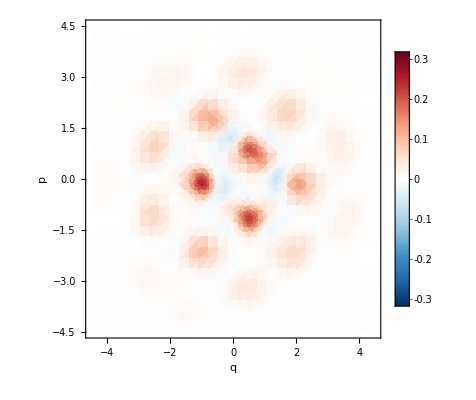

```mathematica
PlotWignerFromDensityMatrix[CodeProjectionOptimizedBosonicN30d2,BlueRed,-1/Pi,1/Pi,30,30]
```

```mathematica
Optimization of qudit-into-an-oscillator code (dim=30) for pure-loss channel
```

```mathematica
γEval=0.1; (*Loss probability*)
dEval=3; (*Dimension of the logical space*)
nEval=30; (*Dimension of the physical space*)
nbarEval=3.; (*Energy constraint*)
```

```mathematica
AlternatingOptimizatingAdjustableIterMax[dEval,nEval,nbarEval,RandomCode[dEval,nEval],PhotonLossChoi[γEval,nEval],10^-6,801,20]
```

{1,0.0941378,0.905862,{{-0.146401+0.280556 ⅈ,0.241343-0.0649555 ⅈ,0.409442-0.159369 ⅈ,0.559879+0.181213 ⅈ,0.129614-0.0367722 ⅈ,0.00260656-0.141743 ⅈ,0.0128416-0.0463698 ⅈ,0.189726+0.172283 ⅈ,0.179763+0.0462358 ⅈ,-0.072049+0.167512 ⅈ,0.0516504-0.0529088 ⅈ,-0.217301+0.0687902 ⅈ,0.0573182+0.0864292 ⅈ,0.13496-0.0829769 ⅈ,0.0480305-0.082505 ⅈ,0.0224608-0.027451 ⅈ,-0.0391002-0.0104074 ⅈ,0.0862325+0.0269074 ⅈ,0.0479811-0.0318635 ⅈ,0.0256807+0.0598229 ⅈ,-0.00410668+0.0032339 ⅈ,0.00540962-0.017008 ⅈ,0.00219706+0.0109792 ⅈ,0.0226994-0.00679919 ⅈ,0.0172094+0.0113883 ⅈ,0.00353338+0.000774602 ⅈ,-0.0188935-0.00226552 ⅈ,0.00247097-0.0248902 ⅈ,0.0184866-0.00253283 ⅈ,-0.0168449-0.00305298 ⅈ},{0.807459-0.0729466 ⅈ,0.289311+0.0103724 ⅈ,0.257144+0.282736 ⅈ,-0.0614484+0.0470392 ⅈ,-0.0321757-0.0143506 ⅈ,0.122827+0.0353118 ⅈ,-0.0580055+0.103202 ⅈ,0.106362+0.100899 ⅈ,0.0525436-0.0315349 ⅈ,-0.0115707+0.0600085 ⅈ,0.00220649+0.00990091 ⅈ,0.0444987-0.0351441 ⅈ,-0.0682878+0.0430961 ⅈ,-0.00335313-0.0967072 ⅈ,-0.0318313+0.0294099 ⅈ,-0.0310727+0.0269697 ⅈ,-0.0468692+0.0222716 ⅈ,-0.0397567+0.03278 ⅈ,0.0385525+0.00700982 ⅈ,0.105998+0.0052915 ⅈ,-0.0081028-0.02532 ⅈ,-0.00218437+0.0263243 ⅈ,0.0261357+0.00808104 ⅈ,-0.00297511-0.0144138 ⅈ,-0.00646418+0.00625507 ⅈ,-0.0126681+0.00426972 ⅈ,-0.0322571+0.00250316 ⅈ,-0.00664468+0.0151687 ⅈ,-0.015508+0.00761076 ⅈ,0.0114067-0.0309239 ⅈ},{-0.309715+0.00574118 ⅈ,0.233811+0.238302 ⅈ,0.405115+0.296318 ⅈ,-0.234145-0.579563 ⅈ,-0.0855629+0.0894633 ⅈ,0.0652887-0.129419 ⅈ,-0.0242156-0.00398482 ⅈ,0.211673-0.127602 ⅈ,0.0714543-0.0622116 ⅈ,-0.010993-0.0131747 ⅈ,-0.0213376+0.0520256 ⅈ,0.0384672+0.00733087 ⅈ,0.114657-0.0282418 ⅈ,0.0292965+0.0339111 ⅈ,-0.0119666-0.00219428 ⅈ,0.0852686-0.0233007 ⅈ,-0.0181024+0.00221255 ⅈ,0.0157526+0.0124375 ⅈ,0.000341685-0.00734949 ⅈ,-0.00677431+0.0102239 ⅈ,-0.0093846+0.0582029 ⅈ,-0.019138-0.0279604 ⅈ,-0.024848-0.0203313 ⅈ,0.0112889-0.0132028 ⅈ,-0.0294459+0.0076267 ⅈ,0.0226497+0.0299814 ⅈ,-0.0132274+0.0232365 ⅈ,0.00424522+0.0288127 ⅈ,-0.0320246+0.000857859 ⅈ,-0.0471065+0. ⅈ}}}

```mathematica
Optimization of qubit-into-5-qubits for amplitude damping channel
```

```mathematica
γEval=0.01;
```

```mathematica
AlternatingOptimizatingAdjustableIterMax[2,2^5,100.,RandomCode[2,2^5],MultiQubitAmplitudeDampingChoi[γEval,5],10^-6,801,20]
```

```mathematica
Optimization of qubit-into-an-oscillator code (dim=30) for dephasing channel
```

```mathematica
VarEval=0.1; (*Variance of dephasing*)
dEval=2; (*Dimension of the logical space*)
nEval=30; (*Dimension of the physical space*)
nbarEval=5.; (*Energy constraint*)
```

```mathematica
RandomCodeEval=RandomCode[dEval,nEval]
```

{{0.116748+0.114922 ⅈ,0.0901619+0.0120591 ⅈ,-0.237956-0.134423 ⅈ,0.219767+0.107269 ⅈ,-0.0685526+0.127521 ⅈ,0.0507836-0.0771755 ⅈ,-0.0147195-0.102677 ⅈ,-0.0929792-0.127032 ⅈ,0.0156581+0.15049 ⅈ,0.0856478-0.127062 ⅈ,-0.000652253+0.108951 ⅈ,-0.0749096+0.0972302 ⅈ,0.0139239+0.179316 ⅈ,0.0684587-0.038304 ⅈ,-0.253294-0.10643 ⅈ,0.0467667-0.0436361 ⅈ,-0.135139-0.0445397 ⅈ,-0.146078+0.0730979 ⅈ,-0.0822903-0.16087 ⅈ,0.0401236+0.193382 ⅈ,-0.0502348-0.102727 ⅈ,-0.125405+0.188444 ⅈ,-0.173404+0.226626 ⅈ,0.0652055+0.11104 ⅈ,0.168138+0.140808 ⅈ,-0.268129+0.238147 ⅈ,0.25579+0.0353718 ⅈ,-0.144226-0.160042 ⅈ,-0.00704893-0.0313339 ⅈ,0.00733438+0.0466285 ⅈ},{0.0540969-0.142177 ⅈ,0.137389+0.0373888 ⅈ,0.0326131+0.149582 ⅈ,0.0704634+0.0721296 ⅈ,-0.149853+0.0414812 ⅈ,0.141396-0.0246548 ⅈ,-0.153722-0.00680704 ⅈ,-0.00920941-0.00913522 ⅈ,0.103617+0.120453 ⅈ,0.0828372-0.171307 ⅈ,-0.213648-0.0104682 ⅈ,-0.363665+0.162243 ⅈ,0.301639-0.0469843 ⅈ,0.00505179+0.0295987 ⅈ,0.0181383-0.204695 ⅈ,0.374354-0.0560687 ⅈ,0.0827658-0.0369832 ⅈ,0.0425699+0.118386 ⅈ,0.147812-0.0421206 ⅈ,0.0424871+0.0551589 ⅈ,-0.0754414+0.117106 ⅈ,0.0677801-0.16416 ⅈ,0.0877271-0.167582 ⅈ,-0.0935586-0.276002 ⅈ,0.0175871-0.0714531 ⅈ,0.128073-0.0176019 ⅈ,0.143863+0.0930006 ⅈ,0.0282199+0.000890579 ⅈ,0.147337-0.0480307 ⅈ,0.0417955-0.0822126 ⅈ}}

```mathematica
AlternatingOptimizatingAdjustableIterMax[dEval,nEval,nbarEval,RandomCodeEval,DephasingChoi[Sqrt[VarEval],nEval],10^-6,401,10]
```

{1,0.0549844,0.945016,{{-0.484617+0.214476 ⅈ,-0.168032+0.184825 ⅈ,0.745791+0.0640393 ⅈ,-0.268225-0.156531 ⅈ},{-0.46104+0.173224 ⅈ,0.107865+0.310839 ⅈ,-0.600664+0.134293 ⅈ,-0.519951+0. ⅈ}}}

{11,0.0114058,0.0774495,{{-0.346623+0.355287 ⅈ,-0.378767+0.175065 ⅈ,0.656735+0.138417 ⅈ,-0.327307-0.148059 ⅈ},{-0.344948-0.0519575 ⅈ,0.34575+0.5669 ⅈ,-0.393121+0.230305 ⅈ,-0.479384+0. ⅈ}}}

{21,0.00558884,0.0584451,{{-0.3149+0.342134 ⅈ,-0.384367+0.208958 ⅈ,0.649102+0.277107 ⅈ,-0.223919-0.21005 ⅈ},{-0.245895-0.15999 ⅈ,0.257386+0.662988 ⅈ,-0.364286+0.260195 ⅈ,-0.455777+0. ⅈ}}}

{31,0.00387999,0.0191045,{{-0.304632+0.331129 ⅈ,-0.388501+0.217175 ⅈ,0.626618+0.355749 ⅈ,-0.149872-0.240389 ⅈ},{-0.181417-0.209111 ⅈ,0.18508+0.698961 ⅈ,-0.362441+0.265265 ⅈ,-0.445904+0. ⅈ}}}

{41,0.00355081,0.00368924,{{-0.301754+0.327807 ⅈ,-0.390474+0.218607 ⅈ,0.610958+0.388965 ⅈ,-0.115218-0.251774 ⅈ},{-0.150903-0.228937 ⅈ,0.150062+0.709594 ⅈ,-0.362362+0.265394 ⅈ,-0.443884+0. ⅈ}}}

{51,0.003495,0.000624617,{{-0.301011+0.326955 ⅈ,-0.391158+0.218885 ⅈ,0.603388+0.402162 ⅈ,-0.100719-0.256168 ⅈ},{-0.138038-0.236874 ⅈ,0.135216+0.712832 ⅈ,-0.362234+0.26515 ⅈ,-0.443741+0. ⅈ}}}

Code not isometry

{61,0.00348576,0.000103479,Null}

{71,0.00348423,0.0000170759,{{-0.300735+0.326645 ⅈ,-0.391485+0.218979 ⅈ,0.598752+0.40954 ⅈ,-0.0923921-0.258624 ⅈ},{-0.130622-0.241373 ⅈ,0.126638+0.714345 ⅈ,-0.362098+0.264946 ⅈ,-0.443891+0. ⅈ}}}

{81,0.00348398,2.818×10^-6,{{-0.30071+0.326618 ⅈ,-0.391519+0.218988 ⅈ,0.598194+0.410396 ⅈ,-0.0914145-0.25891 ⅈ},{-0.129751-0.241899 ⅈ,0.125629+0.714505 ⅈ,-0.362079+0.26492 ⅈ,-0.443921+0. ⅈ}}}